## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)

(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/fourier/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.207662 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 15, 2020, time: 20:42:14

nb: /Users/dantopa/Mathematica_files/nb/ert/rcs/fourier/linear-system-03.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.207662 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
```

## data

### grab slice

```mathematica
rcs=meanRCS[[1]];
m=Length[rcs];
```

```mathematica
Mean[rcs]
```

35.2488

```mathematica
σ=RotateLeft[rcs,180]-Mean[rcs];
```

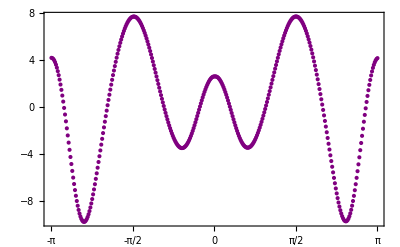

```mathematica
gσ=ListPlot[σ,
Frame->True,
FrameTicks->{{Automatic,Automatic},{{{1,-π},{91,-π/2},{181,0},{271,π/2},{361,π}},Automatic}},PlotStyle->Purple]
```

## 1 compose linear system

```mathematica
A=Table[
θ=(j-181)π/180;
{1,Cos[θ],Cos[2θ],Cos[3θ],Cos[4θ],Cos[5θ],Cos[6θ],Cos[7θ]}
,{j,m}];
```

```mathematica
Dimensions[A]
```

{361,8}

```mathematica
Wx=Simplify[A†.A];
```

```mathematica
Dimensions[Wx]
```

{8,8}

```mathematica
Wxx=FullSimplify[Wx];
%//mf
```

$Aborted

$Aborted

```mathematica
Wx//mf
```

(361 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-1 | 21+4 Cos[π/180]^2+4 Cos[π/90]^2+4 Cos[π/60]^2+4 Cos[π/45]^2+4 Cos[π/36]^2+4 Cos[π/30]^2+4 Cos[(7 π)/180]^2+4 Cos[(2 π)/45]^2+4 Cos[π/20]^2+4 Cos[π/18]^2+4 Cos[(11 π)/180]^2+4 Cos[π/15]^2+4 Cos[(13 π)/180]^2+4 Cos[(7 π)/90]^2+4 Cos[(4 π)/45]^2+4 Cos[(17 π)/180]^2+4 Cos[(19 π)/180]^2+4 Cos[π/9]^2+4 Cos[(7 π)/60]^2+4 Cos[(11 π)/90]^2+4 Cos[(23 π)/180]^2+4 Cos[(2 π)/15]^2+4 Cos[(5 π)/36]^2+4 Cos[(13 π)/90]^2+4 Cos[(3 π)/20]^2+4 Cos[(7 π)/45]^2+4 Cos[(29 π)/180]^2+4 Cos[(31 π)/180]^2+4 Cos[(8 π)/45]^2+4 Cos[(11 π)/60]^2+4 Cos[(17 π)/90]^2+4 Cos[(7 π)/36]^2+4 Cos[(37 π)/180]^2+4 Cos[(19 π)/90]^2+4 Cos[(13 π)/60]^2+4 Cos[(2 π)/9]^2+4 Cos[(41 π)/180]^2+4 Cos[(7 π)/30]^2+4 Cos[(43 π)/180]^2+4 Cos[(11 π)/45]^2+4 Sin[π/180]^2+4 Sin[π/90]^2+4 Sin[π/60]^2+4 Sin[π/45]^2+4 Sin[π/36]^2+4 Sin[π/30]^2+4 Sin[(7 π)/180]^2+4 Sin[(2 π)/45]^2+4 Sin[π/20]^2+4 Sin[π/18]^2+4 Sin[(11 π)/180]^2+4 Sin[π/15]^2+4 Sin[(13 π)/180]^2+4 Sin[(7 π)/90]^2+4 Sin[(4 π)/45]^2+4 Sin[(17 π)/180]^2+4 Sin[(19 π)/180]^2+4 Sin[π/9]^2+4 Sin[(7 π)/60]^2+4 Sin[(11 π)/90]^2+4 Sin[(23 π)/180]^2+4 Sin[(2 π)/15]^2+4 Sin[(5 π)/36]^2+4 Sin[(13 π)/90]^2+4 Sin[(3 π)/20]^2+4 Sin[(7 π)/45]^2+4 Sin[(29 π)/180]^2+4 Sin[(31 π)/180]^2+4 Sin[(8 π)/45]^2+4 Sin[(11 π)/60]^2+4 Sin[(17 π)/90]^2+4 Sin[(7 π)/36]^2+4 Sin[(37 π)/180]^2+4 Sin[(19 π)/90]^2+4 Sin[(13 π)/60]^2+4 Sin[(2 π)/9]^2+4 Sin[(41 π)/180]^2+4 Sin[(7 π)/30]^2+4 Sin[(43 π)/180]^2+4 Sin[(11 π)/45]^2 | -1 | -1+4 Cos[π/180] Cos[π/60]+(√2+√6) Cos[π/36]+√(2 (5+√5)) Cos[π/30]+4 Cos[π/90] Cos[π/30]+4 Cos[π/60] Cos[π/20]+2 √3 Cos[π/18]+Cos[π/15]+√5 Cos[π/15]+4 Cos[π/45] Cos[π/15]+2 Cos[π/9]+4 Cos[(7 π)/180] Cos[(7 π)/60]-Cos[(2 π)/15]+√5 Cos[(2 π)/15]+4 Cos[(2 π)/45] Cos[(2 π)/15]-√2 Cos[(5 π)/36]+√6 Cos[(5 π)/36]+4 Cos[π/20] Cos[(3 π)/20]+4 Cos[(11 π)/180] Cos[(11 π)/60]+√2 Cos[(7 π)/36]-√6 Cos[(7 π)/36]+4 Cos[(13 π)/180] Cos[(13 π)/60]-2 Cos[(2 π)/9]-√(10-2 √5) Cos[(7 π)/30]+4 Cos[(7 π)/90] Cos[(7 π)/30]+4 Cos[(29 π)/180] Sin[π/60]-4 Cos[(31 π)/180] Sin[π/60]-4 Sin[π/180] Sin[π/60]+√2 Sin[π/36]-√6 Sin[π/36]+Sin[π/30]-√5 Sin[π/30]+4 Cos[(7 π)/45] Sin[π/30]-4 Cos[(8 π)/45] Sin[π/30]-4 Sin[π/90] Sin[π/30]+4 Cos[(3 π)/20] Sin[π/20]-4 Cos[(11 π)/60] Sin[π/20]-4 Sin[π/60] Sin[π/20]-2 Sin[π/18]-√(10-2 √5) Sin[π/15]+4 Cos[(13 π)/90] Sin[π/15]-4 Cos[(17 π)/90] Sin[π/15]-4 Sin[π/45] Sin[π/15]-4 Cos[(7 π)/30] Sin[(4 π)/45]-4 Cos[(13 π)/60] Sin[(17 π)/180]-4 Cos[(11 π)/60] Sin[(19 π)/180]-2 √3 Sin[π/9]+4 Cos[(23 π)/180] Sin[(7 π)/60]-4 Cos[(3 π)/20] Sin[(7 π)/60]-4 Cos[(37 π)/180] Sin[(7 π)/60]-4 Sin[(7 π)/180] Sin[(7 π)/60]-4 Cos[(2 π)/15] Sin[(11 π)/90]-4 Cos[(7 π)/60] Sin[(23 π)/180]-√(2 (5+√5)) Sin[(2 π)/15]+4 Cos[(11 π)/90] Sin[(2 π)/15]-4 Cos[(19 π)/90] Sin[(2 π)/15]-4 Sin[(2 π)/45] Sin[(2 π)/15]-√2 Sin[(5 π)/36]-√6 Sin[(5 π)/36]-4 Cos[π/15] Sin[(13 π)/90]-4 Cos[π/20] Sin[(3 π)/20]+4 Cos[(7 π)/60] Sin[(3 π)/20]-4 Cos[(13 π)/60] Sin[(3 π)/20]-4 Sin[π/20] Sin[(3 π)/20]-4 Cos[π/30] Sin[(7 π)/45]-4 Cos[π/60] Sin[(29 π)/180]-4 Cos[π/60] Sin[(31 π)/180]-4 Cos[π/30] Sin[(8 π)/45]-4 Cos[π/20] Sin[(11 π)/60]+4 Cos[(19 π)/180] Sin[(11 π)/60]-4 Cos[(41 π)/180] Sin[(11 π)/60]-4 Sin[(11 π)/180] Sin[(11 π)/60]-4 Cos[π/15] Sin[(17 π)/90]-√2 Sin[(7 π)/36]-√6 Sin[(7 π)/36]-4 Cos[(7 π)/60] Sin[(37 π)/180]-4 Cos[(2 π)/15] Sin[(19 π)/90]+4 Cos[(17 π)/180] Sin[(13 π)/60]-4 Cos[(3 π)/20] Sin[(13 π)/60]-4 Cos[(43 π)/180] Sin[(13 π)/60]-4 Sin[(13 π)/180] Sin[(13 π)/60]-2 √3 Sin[(2 π)/9]-4 Cos[(11 π)/60] Sin[(41 π)/180]-Sin[(7 π)/30]-√5 Sin[(7 π)/30]+4 Cos[(4 π)/45] Sin[(7 π)/30]-4 Cos[(11 π)/45] Sin[(7 π)/30]-4 Sin[(7 π)/90] Sin[(7 π)/30]-4 Cos[(13 π)/60] Sin[(43 π)/180]-4 Cos[(7 π)/30] Sin[(11 π)/45] | -1 | -1+√2 (1+√3) Cos[π/60]+4 Cos[π/180] Cos[π/36]+2 √3 Cos[π/30]+2 √2 Cos[π/20]+4 Cos[π/90] Cos[π/18]+2 Cos[π/15]+4 Cos[π/45] Cos[π/9]-√2 (-1+√3) Cos[(7 π)/60]-2 Cos[(2 π)/15]+4 Cos[π/36] Cos[(5 π)/36]-2 √2 Cos[(3 π)/20]-4 Cos[(5 π)/36] Cos[(31 π)/180]-4 Cos[π/9] Cos[(8 π)/45]-√2 (1+√3) Cos[(11 π)/60]-4 Cos[π/18] Cos[(17 π)/90]-4 Cos[π/36] Cos[(7 π)/36]+4 Cos[(7 π)/180] Cos[(7 π)/36]-4 Cos[(29 π)/180] Cos[(7 π)/36]-4 Cos[π/36] Cos[(37 π)/180]-4 Cos[π/18] Cos[(19 π)/90]-√2 (1+√3) Cos[(13 π)/60]+4 Cos[(2 π)/45] Cos[(2 π)/9]-4 Cos[(7 π)/45] Cos[(2 π)/9]-4 Cos[(5 π)/36] Cos[(41 π)/180]-2 √3 Cos[(7 π)/30]-4 Cos[(7 π)/36] Cos[(43 π)/180]-4 Cos[(2 π)/9] Cos[(11 π)/45]-1/2 Csc[π/18]+1/2 Sec[π/9]+√2 (-1+√3) Sin[π/60]+4 Cos[(17 π)/180] Sin[π/36]-4 Cos[(19 π)/180] Sin[π/36]+4 Sin[π/180] Sin[π/36]+2 Sin[π/30]+2 √2 Sin[π/20]+4 Cos[(4 π)/45] Sin[π/18]-4 Cos[π/9] Sin[π/18]+4 Sin[π/90] Sin[π/18]+4 Cos[(7 π)/36] Sin[(11 π)/180]+2 √3 Sin[π/15]+4 Cos[(5 π)/36] Sin[(13 π)/180]+4 Cos[π/9] Sin[(7 π)/90]+4 Cos[π/18] Sin[(4 π)/45]+4 Cos[π/36] Sin[(17 π)/180]+4 Cos[π/36] Sin[(19 π)/180]+4 Cos[π/18] Sin[π/9]+4 Cos[(7 π)/90] Sin[π/9]-4 Cos[(11 π)/90] Sin[π/9]+4 Sin[π/45] Sin[π/9]+√2 (1+√3) Sin[(7 π)/60]+4 Cos[π/9] Sin[(11 π)/90]+4 Cos[(5 π)/36] Sin[(23 π)/180]+2 √3 Sin[(2 π)/15]+4 Cos[(13 π)/180] Sin[(5 π)/36]-4 Cos[(23 π)/180] Sin[(5 π)/36]+4 Cos[(7 π)/36] Sin[(5 π)/36]+4 Sin[π/36] Sin[(5 π)/36]+4 Cos[(2 π)/9] Sin[(13 π)/90]+2 √2 Sin[(3 π)/20]+4 Sin[(5 π)/36] Sin[(31 π)/180]+4 Sin[π/9] Sin[(8 π)/45]+√2 (-1+√3) Sin[(11 π)/60]+4 Sin[π/18] Sin[(17 π)/90]+4 Cos[(11 π)/180] Sin[(7 π)/36]-4 Cos[(5 π)/36] Sin[(7 π)/36]+4 Sin[π/36] Sin[(7 π)/36]+4 Sin[(7 π)/180] Sin[(7 π)/36]+4 Sin[(29 π)/180] Sin[(7 π)/36]-4 Sin[π/36] Sin[(37 π)/180]-4 Sin[π/18] Sin[(19 π)/90]-√2 (-1+√3) Sin[(13 π)/60]+4 Cos[π/18] Sin[(2 π)/9]-4 Cos[(13 π)/90] Sin[(2 π)/9]+4 Sin[(2 π)/45] Sin[(2 π)/9]-4 Sin[π/9] Sin[(2 π)/9]+4 Sin[(7 π)/45] Sin[(2 π)/9]-4 Sin[(5 π)/36] Sin[(41 π)/180]-2 Sin[(7 π)/30]-4 Sin[(7 π)/36] Sin[(43 π)/180]-4 Sin[(2 π)/9] Sin[(11 π)/45] | -1 | 1/2 (-2+8 Cos[π/60] Cos[(7 π)/60]-8 Cos[(19 π)/180] Cos[(23 π)/180]-8 Cos[π/15] Cos[(2 π)/15]-8 Cos[π/36] Cos[(5 π)/36]+8 Cos[π/90] (Cos[(7 π)/90]-Cos[(13 π)/90])-8 Cos[(11 π)/90] Cos[(13 π)/90]-8 Cos[π/20] Cos[(3 π)/20]+8 Cos[π/45] Cos[(7 π)/45]-8 Cos[(4 π)/45] Cos[(7 π)/45]-8 Cos[(23 π)/180] Cos[(29 π)/180]-8 Cos[(7 π)/60] Cos[(11 π)/60]+8 Cos[π/36] Cos[(7 π)/36]-8 Cos[(31 π)/180] Cos[(37 π)/180]+8 Cos[π/30] Cos[(7 π)/30]-8 Cos[(8 π)/45] Cos[(11 π)/45]-Csc[π/18]+Sec[π/9]-8 Cos[(13 π)/180] Sin[π/180]+8 Cos[(13 π)/60] Sin[π/60]-8 Cos[(19 π)/90] Sin[π/45]+8 Cos[π/15] Sin[π/30]-8 Cos[(41 π)/180] Sin[(7 π)/180]-8 Sin[π/180] Sin[(7 π)/180]-8 Cos[(7 π)/90] Sin[(2 π)/45]-8 Cos[(17 π)/90] Sin[(2 π)/45]-8 Cos[(3 π)/20] Sin[π/20]-8 Cos[π/9] Sin[π/18]-8 Cos[(13 π)/180] Sin[(11 π)/180]-8 Cos[(37 π)/180] Sin[(11 π)/180]-8 Cos[π/30] Sin[π/15]+8 Cos[π/180] (Cos[(7 π)/180]-Sin[(13 π)/180])+8 Cos[(11 π)/180] Sin[(13 π)/180]-8 Cos[(2 π)/45] Sin[(7 π)/90]-8 Sin[π/90] Sin[(7 π)/90]-8 Cos[(11 π)/90] Sin[(4 π)/45]-8 Cos[(29 π)/180] Sin[(17 π)/180]+8 Cos[(41 π)/180] Sin[(17 π)/180]-8 Cos[(43 π)/180] Sin[(19 π)/180]+8 Cos[π/18] Sin[π/9]-8 Sin[π/60] Sin[(7 π)/60]-8 Cos[(4 π)/45] Sin[(11 π)/90]-8 Sin[(19 π)/180] Sin[(23 π)/180]+8 Cos[(7 π)/30] Sin[(2 π)/15]-8 Sin[π/15] Sin[(2 π)/15]-8 Cos[(7 π)/36] Sin[(5 π)/36]-8 Sin[π/36] Sin[(5 π)/36]+8 Sin[π/90] Sin[(13 π)/90]-8 Sin[(11 π)/90] Sin[(13 π)/90]+8 Cos[π/20] Sin[(3 π)/20]+8 Sin[π/20] Sin[(3 π)/20]-8 Sin[π/45] Sin[(7 π)/45]+8 Sin[(4 π)/45] Sin[(7 π)/45]-8 Cos[(17 π)/180] Sin[(29 π)/180]+8 Sin[(23 π)/180] Sin[(29 π)/180]+8 Cos[(43 π)/180] Sin[(31 π)/180]-8 Cos[(17 π)/90] Sin[(8 π)/45]+8 Cos[(13 π)/60] Sin[(11 π)/60]-8 Sin[(7 π)/60] Sin[(11 π)/60]+8 Cos[(2 π)/45] Sin[(17 π)/90]+8 Cos[(8 π)/45] Sin[(17 π)/90]+8 Cos[(5 π)/36] Sin[(7 π)/36]-8 Sin[π/36] Sin[(7 π)/36]+8 Cos[(11 π)/180] Sin[(37 π)/180]+8 Sin[(31 π)/180] Sin[(37 π)/180]+8 Cos[π/45] Sin[(19 π)/90]+8 Cos[(11 π)/45] Sin[(19 π)/90]+8 Cos[π/60] Sin[(13 π)/60]-8 Cos[(11 π)/60] Sin[(13 π)/60]+8 Cos[π/18] Sin[(2 π)/9]-8 Sin[π/9] Sin[(2 π)/9]+8 Cos[(7 π)/180] Sin[(41 π)/180]+8 Cos[(17 π)/180] Sin[(41 π)/180]+8 Cos[(2 π)/15] Sin[(7 π)/30]-8 Sin[π/30] Sin[(7 π)/30]-8 Cos[(19 π)/180] Sin[(43 π)/180]+8 Cos[(31 π)/180] Sin[(43 π)/180]+8 Cos[(19 π)/90] Sin[(11 π)/45]+8 Sin[(8 π)/45] Sin[(11 π)/45])
1 | -1 | 181 | -1 | 1 | -1 | -3-8 Cos[π/45]+8 Cos[(2 π)/45]+4 √3 Cos[π/18]+2 Cos[π/15]+2 √5 Cos[π/15]+8 Cos[(4 π)/45]+4 Cos[π/9]-2 Cos[(2 π)/15]+2 √5 Cos[(2 π)/15]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]-4 Cos[(2 π)/9]-2 √(10-2 √5) Cos[(7 π)/30]-8 Cos[(11 π)/45]+8 Sin[π/90]+2 Sin[π/30]-2 √5 Sin[π/30]-4 Sin[π/18]-2 √(10-2 √5) Sin[π/15]-8 Sin[(7 π)/90]-4 √3 Sin[π/9]-8 Sin[(11 π)/90]+2 √(2 (5+√5)) (Cos[π/30]-Sin[(2 π)/15])+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]-8 Sin[(19 π)/90]-4 √3 Sin[(2 π)/9]-2 Sin[(7 π)/30]-2 √5 Sin[(7 π)/30] | -1
-1 | -1+4 Cos[π/180] Cos[π/60]+(√2+√6) Cos[π/36]+√(2 (5+√5)) Cos[π/30]+4 Cos[π/90] Cos[π/30]+4 Cos[π/60] Cos[π/20]+2 √3 Cos[π/18]+Cos[π/15]+√5 Cos[π/15]+4 Cos[π/45] Cos[π/15]+2 Cos[π/9]+4 Cos[(7 π)/180] Cos[(7 π)/60]-Cos[(2 π)/15]+√5 Cos[(2 π)/15]+4 Cos[(2 π)/45] Cos[(2 π)/15]-√2 Cos[(5 π)/36]+√6 Cos[(5 π)/36]+4 Cos[π/20] Cos[(3 π)/20]+4 Cos[(11 π)/180] Cos[(11 π)/60]+√2 Cos[(7 π)/36]-√6 Cos[(7 π)/36]+4 Cos[(13 π)/180] Cos[(13 π)/60]-2 Cos[(2 π)/9]-√(10-2 √5) Cos[(7 π)/30]+4 Cos[(7 π)/90] Cos[(7 π)/30]+4 Cos[(29 π)/180] Sin[π/60]-4 Cos[(31 π)/180] Sin[π/60]-4 Sin[π/180] Sin[π/60]+√2 Sin[π/36]-√6 Sin[π/36]+Sin[π/30]-√5 Sin[π/30]+4 Cos[(7 π)/45] Sin[π/30]-4 Cos[(8 π)/45] Sin[π/30]-4 Sin[π/90] Sin[π/30]+4 Cos[(3 π)/20] Sin[π/20]-4 Cos[(11 π)/60] Sin[π/20]-4 Sin[π/60] Sin[π/20]-2 Sin[π/18]-√(10-2 √5) Sin[π/15]+4 Cos[(13 π)/90] Sin[π/15]-4 Cos[(17 π)/90] Sin[π/15]-4 Sin[π/45] Sin[π/15]-4 Cos[(7 π)/30] Sin[(4 π)/45]-4 Cos[(13 π)/60] Sin[(17 π)/180]-4 Cos[(11 π)/60] Sin[(19 π)/180]-2 √3 Sin[π/9]+4 Cos[(23 π)/180] Sin[(7 π)/60]-4 Cos[(3 π)/20] Sin[(7 π)/60]-4 Cos[(37 π)/180] Sin[(7 π)/60]-4 Sin[(7 π)/180] Sin[(7 π)/60]-4 Cos[(2 π)/15] Sin[(11 π)/90]-4 Cos[(7 π)/60] Sin[(23 π)/180]-√(2 (5+√5)) Sin[(2 π)/15]+4 Cos[(11 π)/90] Sin[(2 π)/15]-4 Cos[(19 π)/90] Sin[(2 π)/15]-4 Sin[(2 π)/45] Sin[(2 π)/15]-√2 Sin[(5 π)/36]-√6 Sin[(5 π)/36]-4 Cos[π/15] Sin[(13 π)/90]-4 Cos[π/20] Sin[(3 π)/20]+4 Cos[(7 π)/60] Sin[(3 π)/20]-4 Cos[(13 π)/60] Sin[(3 π)/20]-4 Sin[π/20] Sin[(3 π)/20]-4 Cos[π/30] Sin[(7 π)/45]-4 Cos[π/60] Sin[(29 π)/180]-4 Cos[π/60] Sin[(31 π)/180]-4 Cos[π/30] Sin[(8 π)/45]-4 Cos[π/20] Sin[(11 π)/60]+4 Cos[(19 π)/180] Sin[(11 π)/60]-4 Cos[(41 π)/180] Sin[(11 π)/60]-4 Sin[(11 π)/180] Sin[(11 π)/60]-4 Cos[π/15] Sin[(17 π)/90]-√2 Sin[(7 π)/36]-√6 Sin[(7 π)/36]-4 Cos[(7 π)/60] Sin[(37 π)/180]-4 Cos[(2 π)/15] Sin[(19 π)/90]+4 Cos[(17 π)/180] Sin[(13 π)/60]-4 Cos[(3 π)/20] Sin[(13 π)/60]-4 Cos[(43 π)/180] Sin[(13 π)/60]-4 Sin[(13 π)/180] Sin[(13 π)/60]-2 √3 Sin[(2 π)/9]-4 Cos[(11 π)/60] Sin[(41 π)/180]-Sin[(7 π)/30]-√5 Sin[(7 π)/30]+4 Cos[(4 π)/45] Sin[(7 π)/30]-4 Cos[(11 π)/45] Sin[(7 π)/30]-4 Sin[(7 π)/90] Sin[(7 π)/30]-4 Cos[(13 π)/60] Sin[(43 π)/180]-4 Cos[(7 π)/30] Sin[(11 π)/45] | -1 | 181 | -1 | 1-8 Cos[π/45]+√2 (-1+√3) Cos[π/36]+8 Cos[(2 π)/45]-2 √3 Cos[π/18]+8 Cos[(4 π)/45]+2 Cos[π/9]+√2 Cos[(5 π)/36]+√6 Cos[(5 π)/36]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]-√2 Cos[(7 π)/36]-√6 Cos[(7 π)/36]-2 Cos[(2 π)/9]-8 Cos[(11 π)/45]+8 Sin[π/90]-√2 Sin[π/36]-√6 Sin[π/36]-2 Sin[π/18]-8 Sin[(7 π)/90]+2 √3 Sin[π/9]-8 Sin[(11 π)/90]+√2 Sin[(5 π)/36]-√6 Sin[(5 π)/36]+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]+√2 Sin[(7 π)/36]-√6 Sin[(7 π)/36]-8 Sin[(19 π)/90]+2 √3 Sin[(2 π)/9] | -1 | 1+(√2-√6) Cos[π/36]+4 Cos[π/60] Cos[(7 π)/180]-2 √3 Cos[π/18]+Cos[π/15]-√5 Cos[π/15]+4 Cos[π/30] Cos[(7 π)/90]+4 Cos[π/20] Cos[(7 π)/60]-4 Cos[(11 π)/180] Cos[(7 π)/60]-Cos[(2 π)/15]-√5 Cos[(2 π)/15]-√2 Cos[(5 π)/36]-√6 Cos[(5 π)/36]-4 Cos[π/60] Cos[(3 π)/20]-2 Cos[(7 π)/45]+4 Cos[π/15] Cos[(7 π)/45]-4 Cos[π/15] Cos[(8 π)/45]-4 Cos[(17 π)/180] Cos[(11 π)/60]+√2 Cos[(7 π)/36]+√6 Cos[(7 π)/36]-4 Cos[π/20] Cos[(13 π)/60]+4 Cos[(29 π)/180] Cos[(13 π)/60]-4 Cos[(31 π)/180] Cos[(13 π)/60]-2 Cos[(2 π)/9]+√(2 (5+√5)) Cos[(7 π)/30]+4 Cos[(11 π)/90] Cos[(7 π)/30]-4 Cos[(19 π)/90] Cos[(7 π)/30]+4 Cos[(11 π)/60] Cos[(43 π)/180]-4 Cos[(13 π)/60] Sin[π/180]-4 Cos[π/15] Sin[π/90]-4 Cos[(23 π)/180] Sin[π/60]+4 Cos[(37 π)/180] Sin[π/60]+√2 Sin[π/36]+√6 Sin[π/36]+Sin[π/30]+√5 Sin[π/30]-4 Cos[(4 π)/45] Sin[π/30]+4 Cos[(11 π)/45] Sin[π/30]+4 Sin[π/60] Sin[(7 π)/180]-4 Cos[(7 π)/30] Sin[(2 π)/45]-2 Sin[π/18]+√(2 (5+√5)) Sin[π/15]-4 Cos[π/90] Sin[π/15]+4 Cos[(11 π)/60] Sin[(13 π)/180]+4 Sin[π/30] Sin[(7 π)/90]-4 Cos[π/30] Sin[(4 π)/45]+4 Cos[(7 π)/60] Sin[(19 π)/180]+2 √3 Sin[π/9]-4 Cos[(19 π)/180] Sin[(7 π)/60]+4 Cos[(41 π)/180] Sin[(7 π)/60]+4 Sin[π/20] Sin[(7 π)/60]+4 Sin[(11 π)/180] Sin[(7 π)/60]-4 Cos[π/60] Sin[(23 π)/180]+√(10-2 √5) (Cos[π/30]-Sin[(2 π)/15])-4 Cos[(13 π)/90] Sin[(2 π)/15]+4 Cos[(17 π)/90] Sin[(2 π)/15]+4 Sin[π/45] Sin[(2 π)/15]-√2 Sin[(5 π)/36]+√6 Sin[(5 π)/36]+4 Cos[(2 π)/15] Sin[(13 π)/90]-4 Cos[(11 π)/60] Sin[(3 π)/20]-4 Sin[π/60] Sin[(3 π)/20]+4 Sin[π/15] Sin[(7 π)/45]+4 Sin[π/15] Sin[(8 π)/45]+4 Cos[(13 π)/180] Sin[(11 π)/60]+4 Cos[(3 π)/20] Sin[(11 π)/60]-4 Sin[(17 π)/180] Sin[(11 π)/60]+4 Cos[(2 π)/15] Sin[(17 π)/90]-√2 Sin[(7 π)/36]+√6 Sin[(7 π)/36]-4 Cos[π/60] Sin[(37 π)/180]+4 Cos[π/180] Sin[(13 π)/60]+4 Sin[π/20] Sin[(13 π)/60]-4 Sin[(29 π)/180] Sin[(13 π)/60]-4 Sin[(31 π)/180] Sin[(13 π)/60]+2 √3 Sin[(2 π)/9]+4 Cos[(7 π)/60] Sin[(41 π)/180]-Sin[(7 π)/30]+√5 Sin[(7 π)/30]+4 Cos[(2 π)/45] Sin[(7 π)/30]-4 Sin[(11 π)/90] Sin[(7 π)/30]-4 Sin[(19 π)/90] Sin[(7 π)/30]-4 Sin[(11 π)/60] Sin[(43 π)/180]-4 Cos[π/30] Sin[(11 π)/45]
1 | -1 | 1 | -1 | 177-8 Cos[π/45]+8 Cos[(2 π)/45]-8 Cos[π/15]+8 Cos[(4 π)/45]-8 Cos[π/9]+8 Cos[(2 π)/15]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]+8 Cos[(2 π)/9]-8 Cos[(11 π)/45]+8 Sin[π/90]-8 Sin[π/30]+8 Sin[π/18]-8 Sin[(7 π)/90]-8 Sin[(11 π)/90]+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]-8 Sin[(19 π)/90]+8 Sin[(7 π)/30] | -1 | 1 | -1
-1 | -1+√2 (1+√3) Cos[π/60]+4 Cos[π/180] Cos[π/36]+2 √3 Cos[π/30]+2 √2 Cos[π/20]+4 Cos[π/90] Cos[π/18]+2 Cos[π/15]+4 Cos[π/45] Cos[π/9]-√2 (-1+√3) Cos[(7 π)/60]-2 Cos[(2 π)/15]+4 Cos[π/36] Cos[(5 π)/36]-2 √2 Cos[(3 π)/20]-4 Cos[(5 π)/36] Cos[(31 π)/180]-4 Cos[π/9] Cos[(8 π)/45]-√2 (1+√3) Cos[(11 π)/60]-4 Cos[π/18] Cos[(17 π)/90]-4 Cos[π/36] Cos[(7 π)/36]+4 Cos[(7 π)/180] Cos[(7 π)/36]-4 Cos[(29 π)/180] Cos[(7 π)/36]-4 Cos[π/36] Cos[(37 π)/180]-4 Cos[π/18] Cos[(19 π)/90]-√2 (1+√3) Cos[(13 π)/60]+4 Cos[(2 π)/45] Cos[(2 π)/9]-4 Cos[(7 π)/45] Cos[(2 π)/9]-4 Cos[(5 π)/36] Cos[(41 π)/180]-2 √3 Cos[(7 π)/30]-4 Cos[(7 π)/36] Cos[(43 π)/180]-4 Cos[(2 π)/9] Cos[(11 π)/45]-1/2 Csc[π/18]+1/2 Sec[π/9]+√2 (-1+√3) Sin[π/60]+4 Cos[(17 π)/180] Sin[π/36]-4 Cos[(19 π)/180] Sin[π/36]+4 Sin[π/180] Sin[π/36]+2 Sin[π/30]+2 √2 Sin[π/20]+4 Cos[(4 π)/45] Sin[π/18]-4 Cos[π/9] Sin[π/18]+4 Sin[π/90] Sin[π/18]+4 Cos[(7 π)/36] Sin[(11 π)/180]+2 √3 Sin[π/15]+4 Cos[(5 π)/36] Sin[(13 π)/180]+4 Cos[π/9] Sin[(7 π)/90]+4 Cos[π/18] Sin[(4 π)/45]+4 Cos[π/36] Sin[(17 π)/180]+4 Cos[π/36] Sin[(19 π)/180]+4 Cos[π/18] Sin[π/9]+4 Cos[(7 π)/90] Sin[π/9]-4 Cos[(11 π)/90] Sin[π/9]+4 Sin[π/45] Sin[π/9]+√2 (1+√3) Sin[(7 π)/60]+4 Cos[π/9] Sin[(11 π)/90]+4 Cos[(5 π)/36] Sin[(23 π)/180]+2 √3 Sin[(2 π)/15]+4 Cos[(13 π)/180] Sin[(5 π)/36]-4 Cos[(23 π)/180] Sin[(5 π)/36]+4 Cos[(7 π)/36] Sin[(5 π)/36]+4 Sin[π/36] Sin[(5 π)/36]+4 Cos[(2 π)/9] Sin[(13 π)/90]+2 √2 Sin[(3 π)/20]+4 Sin[(5 π)/36] Sin[(31 π)/180]+4 Sin[π/9] Sin[(8 π)/45]+√2 (-1+√3) Sin[(11 π)/60]+4 Sin[π/18] Sin[(17 π)/90]+4 Cos[(11 π)/180] Sin[(7 π)/36]-4 Cos[(5 π)/36] Sin[(7 π)/36]+4 Sin[π/36] Sin[(7 π)/36]+4 Sin[(7 π)/180] Sin[(7 π)/36]+4 Sin[(29 π)/180] Sin[(7 π)/36]-4 Sin[π/36] Sin[(37 π)/180]-4 Sin[π/18] Sin[(19 π)/90]-√2 (-1+√3) Sin[(13 π)/60]+4 Cos[π/18] Sin[(2 π)/9]-4 Cos[(13 π)/90] Sin[(2 π)/9]+4 Sin[(2 π)/45] Sin[(2 π)/9]-4 Sin[π/9] Sin[(2 π)/9]+4 Sin[(7 π)/45] Sin[(2 π)/9]-4 Sin[(5 π)/36] Sin[(41 π)/180]-2 Sin[(7 π)/30]-4 Sin[(7 π)/36] Sin[(43 π)/180]-4 Sin[(2 π)/9] Sin[(11 π)/45] | -1 | 1-8 Cos[π/45]+√2 (-1+√3) Cos[π/36]+8 Cos[(2 π)/45]-2 √3 Cos[π/18]+8 Cos[(4 π)/45]+2 Cos[π/9]+√2 Cos[(5 π)/36]+√6 Cos[(5 π)/36]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]-√2 Cos[(7 π)/36]-√6 Cos[(7 π)/36]-2 Cos[(2 π)/9]-8 Cos[(11 π)/45]+8 Sin[π/90]-√2 Sin[π/36]-√6 Sin[π/36]-2 Sin[π/18]-8 Sin[(7 π)/90]+2 √3 Sin[π/9]-8 Sin[(11 π)/90]+√2 Sin[(5 π)/36]-√6 Sin[(5 π)/36]+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]+√2 Sin[(7 π)/36]-√6 Sin[(7 π)/36]-8 Sin[(19 π)/90]+2 √3 Sin[(2 π)/9] | -1 | 181 | -1 | 1-√2 (-1+√3) Cos[π/60]-2 √3 Cos[π/30]+4 Cos[π/36] Cos[(7 π)/180]+2 √2 Cos[π/20]+2 Cos[π/15]+4 Cos[π/18] Cos[(7 π)/90]-4 Cos[(2 π)/45] Cos[π/9]+√2 (1+√3) Cos[(7 π)/60]-4 Cos[π/18] Cos[(11 π)/90]-2 Cos[(2 π)/15]-4 Cos[π/180] Cos[(5 π)/36]-2 √2 Cos[(3 π)/20]+4 Cos[π/9] Cos[(7 π)/45]-4 Cos[π/36] Cos[(29 π)/180]+√2 (-1+√3) Cos[(11 π)/60]-4 Cos[(13 π)/180] Cos[(7 π)/36]+4 Cos[(23 π)/180] Cos[(7 π)/36]+4 Cos[(5 π)/36] Cos[(7 π)/36]+4 Cos[(5 π)/36] Cos[(37 π)/180]+√2 (-1+√3) Cos[(13 π)/60]+4 Cos[(4 π)/45] Cos[(2 π)/9]+2 √3 Cos[(7 π)/30]-4 Cos[π/36] Cos[(43 π)/180]+4 Cos[π/9] Cos[(11 π)/45]-1/2 Csc[π/18]+1/2 Sec[π/9]+4 Cos[(2 π)/9] Sin[π/90]-√2 (1+√3) Sin[π/60]+4 Cos[π/18] Sin[π/45]-4 Cos[(11 π)/180] Sin[π/36]+4 Cos[(5 π)/36] Sin[π/36]-4 Cos[(7 π)/36] Sin[π/36]+2 Sin[π/30]-4 Sin[π/36] Sin[(7 π)/180]+2 √2 Sin[π/20]-4 Cos[π/45] Sin[π/18]-4 Cos[π/9] Sin[π/18]+4 Cos[(8 π)/45] Sin[π/18]+4 Cos[π/36] Sin[(11 π)/180]-2 √3 Sin[π/15]-4 Sin[π/18] Sin[(7 π)/90]-4 Cos[(5 π)/36] Sin[(17 π)/180]-4 Cos[(5 π)/36] Sin[(19 π)/180]+2 Sin[π/9]-4 Cos[π/18] Sin[π/9]+4 Cos[(13 π)/90] Sin[π/9]-4 Sin[(2 π)/45] Sin[π/9]-√2 (-1+√3) Sin[(7 π)/60]-4 Sin[π/18] Sin[(11 π)/90]-2 √3 Sin[(2 π)/15]-4 Cos[(17 π)/180] Sin[(5 π)/36]+4 Cos[(19 π)/180] Sin[(5 π)/36]-4 Sin[π/180] Sin[(5 π)/36]-4 Cos[π/9] Sin[(13 π)/90]+2 √2 Sin[(3 π)/20]-4 Sin[π/9] Sin[(7 π)/45]-4 Sin[π/36] Sin[(29 π)/180]-4 Cos[(7 π)/36] Sin[(31 π)/180]+4 Cos[π/18] Sin[(8 π)/45]-√2 (1+√3) Sin[(11 π)/60]+4 Cos[(2 π)/9] Sin[(17 π)/90]-4 Cos[(31 π)/180] Sin[(7 π)/36]-4 Cos[(41 π)/180] Sin[(7 π)/36]+4 Sin[(13 π)/180] Sin[(7 π)/36]+4 Sin[(23 π)/180] Sin[(7 π)/36]-4 Sin[(5 π)/36] Sin[(7 π)/36]+4 Sin[(5 π)/36] Sin[(37 π)/180]-4 Cos[(2 π)/9] Sin[(19 π)/90]+√2 (1+√3) Sin[(13 π)/60]+2 Sin[(2 π)/9]+4 Cos[π/90] Sin[(2 π)/9]-4 Cos[π/18] Sin[(2 π)/9]-4 Cos[(17 π)/90] Sin[(2 π)/9]-4 Cos[(19 π)/90] Sin[(2 π)/9]+4 Sin[(4 π)/45] Sin[(2 π)/9]+4 Sin[π/9] Sin[(2 π)/9]+4 Cos[(7 π)/36] Sin[(41 π)/180]-2 Sin[(7 π)/30]+4 Sin[π/36] Sin[(43 π)/180]+4 Sin[π/9] Sin[(11 π)/45]
1 | -1 | -3-8 Cos[π/45]+8 Cos[(2 π)/45]+4 √3 Cos[π/18]+2 Cos[π/15]+2 √5 Cos[π/15]+8 Cos[(4 π)/45]+4 Cos[π/9]-2 Cos[(2 π)/15]+2 √5 Cos[(2 π)/15]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]-4 Cos[(2 π)/9]-2 √(10-2 √5) Cos[(7 π)/30]-8 Cos[(11 π)/45]+8 Sin[π/90]+2 Sin[π/30]-2 √5 Sin[π/30]-4 Sin[π/18]-2 √(10-2 √5) Sin[π/15]-8 Sin[(7 π)/90]-4 √3 Sin[π/9]-8 Sin[(11 π)/90]+2 √(2 (5+√5)) (Cos[π/30]-Sin[(2 π)/15])+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]-8 Sin[(19 π)/90]-4 √3 Sin[(2 π)/9]-2 Sin[(7 π)/30]-2 √5 Sin[(7 π)/30] | -1 | 1 | -1 | 181 | -1
-1 | 1/2 (-2+8 Cos[π/60] Cos[(7 π)/60]-8 Cos[(19 π)/180] Cos[(23 π)/180]-8 Cos[π/15] Cos[(2 π)/15]-8 Cos[π/36] Cos[(5 π)/36]+8 Cos[π/90] (Cos[(7 π)/90]-Cos[(13 π)/90])-8 Cos[(11 π)/90] Cos[(13 π)/90]-8 Cos[π/20] Cos[(3 π)/20]+8 Cos[π/45] Cos[(7 π)/45]-8 Cos[(4 π)/45] Cos[(7 π)/45]-8 Cos[(23 π)/180] Cos[(29 π)/180]-8 Cos[(7 π)/60] Cos[(11 π)/60]+8 Cos[π/36] Cos[(7 π)/36]-8 Cos[(31 π)/180] Cos[(37 π)/180]+8 Cos[π/30] Cos[(7 π)/30]-8 Cos[(8 π)/45] Cos[(11 π)/45]-Csc[π/18]+Sec[π/9]-8 Cos[(13 π)/180] Sin[π/180]+8 Cos[(13 π)/60] Sin[π/60]-8 Cos[(19 π)/90] Sin[π/45]+8 Cos[π/15] Sin[π/30]-8 Cos[(41 π)/180] Sin[(7 π)/180]-8 Sin[π/180] Sin[(7 π)/180]-8 Cos[(7 π)/90] Sin[(2 π)/45]-8 Cos[(17 π)/90] Sin[(2 π)/45]-8 Cos[(3 π)/20] Sin[π/20]-8 Cos[π/9] Sin[π/18]-8 Cos[(13 π)/180] Sin[(11 π)/180]-8 Cos[(37 π)/180] Sin[(11 π)/180]-8 Cos[π/30] Sin[π/15]+8 Cos[π/180] (Cos[(7 π)/180]-Sin[(13 π)/180])+8 Cos[(11 π)/180] Sin[(13 π)/180]-8 Cos[(2 π)/45] Sin[(7 π)/90]-8 Sin[π/90] Sin[(7 π)/90]-8 Cos[(11 π)/90] Sin[(4 π)/45]-8 Cos[(29 π)/180] Sin[(17 π)/180]+8 Cos[(41 π)/180] Sin[(17 π)/180]-8 Cos[(43 π)/180] Sin[(19 π)/180]+8 Cos[π/18] Sin[π/9]-8 Sin[π/60] Sin[(7 π)/60]-8 Cos[(4 π)/45] Sin[(11 π)/90]-8 Sin[(19 π)/180] Sin[(23 π)/180]+8 Cos[(7 π)/30] Sin[(2 π)/15]-8 Sin[π/15] Sin[(2 π)/15]-8 Cos[(7 π)/36] Sin[(5 π)/36]-8 Sin[π/36] Sin[(5 π)/36]+8 Sin[π/90] Sin[(13 π)/90]-8 Sin[(11 π)/90] Sin[(13 π)/90]+8 Cos[π/20] Sin[(3 π)/20]+8 Sin[π/20] Sin[(3 π)/20]-8 Sin[π/45] Sin[(7 π)/45]+8 Sin[(4 π)/45] Sin[(7 π)/45]-8 Cos[(17 π)/180] Sin[(29 π)/180]+8 Sin[(23 π)/180] Sin[(29 π)/180]+8 Cos[(43 π)/180] Sin[(31 π)/180]-8 Cos[(17 π)/90] Sin[(8 π)/45]+8 Cos[(13 π)/60] Sin[(11 π)/60]-8 Sin[(7 π)/60] Sin[(11 π)/60]+8 Cos[(2 π)/45] Sin[(17 π)/90]+8 Cos[(8 π)/45] Sin[(17 π)/90]+8 Cos[(5 π)/36] Sin[(7 π)/36]-8 Sin[π/36] Sin[(7 π)/36]+8 Cos[(11 π)/180] Sin[(37 π)/180]+8 Sin[(31 π)/180] Sin[(37 π)/180]+8 Cos[π/45] Sin[(19 π)/90]+8 Cos[(11 π)/45] Sin[(19 π)/90]+8 Cos[π/60] Sin[(13 π)/60]-8 Cos[(11 π)/60] Sin[(13 π)/60]+8 Cos[π/18] Sin[(2 π)/9]-8 Sin[π/9] Sin[(2 π)/9]+8 Cos[(7 π)/180] Sin[(41 π)/180]+8 Cos[(17 π)/180] Sin[(41 π)/180]+8 Cos[(2 π)/15] Sin[(7 π)/30]-8 Sin[π/30] Sin[(7 π)/30]-8 Cos[(19 π)/180] Sin[(43 π)/180]+8 Cos[(31 π)/180] Sin[(43 π)/180]+8 Cos[(19 π)/90] Sin[(11 π)/45]+8 Sin[(8 π)/45] Sin[(11 π)/45]) | -1 | 1+(√2-√6) Cos[π/36]+4 Cos[π/60] Cos[(7 π)/180]-2 √3 Cos[π/18]+Cos[π/15]-√5 Cos[π/15]+4 Cos[π/30] Cos[(7 π)/90]+4 Cos[π/20] Cos[(7 π)/60]-4 Cos[(11 π)/180] Cos[(7 π)/60]-Cos[(2 π)/15]-√5 Cos[(2 π)/15]-√2 Cos[(5 π)/36]-√6 Cos[(5 π)/36]-4 Cos[π/60] Cos[(3 π)/20]-2 Cos[(7 π)/45]+4 Cos[π/15] Cos[(7 π)/45]-4 Cos[π/15] Cos[(8 π)/45]-4 Cos[(17 π)/180] Cos[(11 π)/60]+√2 Cos[(7 π)/36]+√6 Cos[(7 π)/36]-4 Cos[π/20] Cos[(13 π)/60]+4 Cos[(29 π)/180] Cos[(13 π)/60]-4 Cos[(31 π)/180] Cos[(13 π)/60]-2 Cos[(2 π)/9]+√(2 (5+√5)) Cos[(7 π)/30]+4 Cos[(11 π)/90] Cos[(7 π)/30]-4 Cos[(19 π)/90] Cos[(7 π)/30]+4 Cos[(11 π)/60] Cos[(43 π)/180]-4 Cos[(13 π)/60] Sin[π/180]-4 Cos[π/15] Sin[π/90]-4 Cos[(23 π)/180] Sin[π/60]+4 Cos[(37 π)/180] Sin[π/60]+√2 Sin[π/36]+√6 Sin[π/36]+Sin[π/30]+√5 Sin[π/30]-4 Cos[(4 π)/45] Sin[π/30]+4 Cos[(11 π)/45] Sin[π/30]+4 Sin[π/60] Sin[(7 π)/180]-4 Cos[(7 π)/30] Sin[(2 π)/45]-2 Sin[π/18]+√(2 (5+√5)) Sin[π/15]-4 Cos[π/90] Sin[π/15]+4 Cos[(11 π)/60] Sin[(13 π)/180]+4 Sin[π/30] Sin[(7 π)/90]-4 Cos[π/30] Sin[(4 π)/45]+4 Cos[(7 π)/60] Sin[(19 π)/180]+2 √3 Sin[π/9]-4 Cos[(19 π)/180] Sin[(7 π)/60]+4 Cos[(41 π)/180] Sin[(7 π)/60]+4 Sin[π/20] Sin[(7 π)/60]+4 Sin[(11 π)/180] Sin[(7 π)/60]-4 Cos[π/60] Sin[(23 π)/180]+√(10-2 √5) (Cos[π/30]-Sin[(2 π)/15])-4 Cos[(13 π)/90] Sin[(2 π)/15]+4 Cos[(17 π)/90] Sin[(2 π)/15]+4 Sin[π/45] Sin[(2 π)/15]-√2 Sin[(5 π)/36]+√6 Sin[(5 π)/36]+4 Cos[(2 π)/15] Sin[(13 π)/90]-4 Cos[(11 π)/60] Sin[(3 π)/20]-4 Sin[π/60] Sin[(3 π)/20]+4 Sin[π/15] Sin[(7 π)/45]+4 Sin[π/15] Sin[(8 π)/45]+4 Cos[(13 π)/180] Sin[(11 π)/60]+4 Cos[(3 π)/20] Sin[(11 π)/60]-4 Sin[(17 π)/180] Sin[(11 π)/60]+4 Cos[(2 π)/15] Sin[(17 π)/90]-√2 Sin[(7 π)/36]+√6 Sin[(7 π)/36]-4 Cos[π/60] Sin[(37 π)/180]+4 Cos[π/180] Sin[(13 π)/60]+4 Sin[π/20] Sin[(13 π)/60]-4 Sin[(29 π)/180] Sin[(13 π)/60]-4 Sin[(31 π)/180] Sin[(13 π)/60]+2 √3 Sin[(2 π)/9]+4 Cos[(7 π)/60] Sin[(41 π)/180]-Sin[(7 π)/30]+√5 Sin[(7 π)/30]+4 Cos[(2 π)/45] Sin[(7 π)/30]-4 Sin[(11 π)/90] Sin[(7 π)/30]-4 Sin[(19 π)/90] Sin[(7 π)/30]-4 Sin[(11 π)/60] Sin[(43 π)/180]-4 Cos[π/30] Sin[(11 π)/45] | -1 | 1-√2 (-1+√3) Cos[π/60]-2 √3 Cos[π/30]+4 Cos[π/36] Cos[(7 π)/180]+2 √2 Cos[π/20]+2 Cos[π/15]+4 Cos[π/18] Cos[(7 π)/90]-4 Cos[(2 π)/45] Cos[π/9]+√2 (1+√3) Cos[(7 π)/60]-4 Cos[π/18] Cos[(11 π)/90]-2 Cos[(2 π)/15]-4 Cos[π/180] Cos[(5 π)/36]-2 √2 Cos[(3 π)/20]+4 Cos[π/9] Cos[(7 π)/45]-4 Cos[π/36] Cos[(29 π)/180]+√2 (-1+√3) Cos[(11 π)/60]-4 Cos[(13 π)/180] Cos[(7 π)/36]+4 Cos[(23 π)/180] Cos[(7 π)/36]+4 Cos[(5 π)/36] Cos[(7 π)/36]+4 Cos[(5 π)/36] Cos[(37 π)/180]+√2 (-1+√3) Cos[(13 π)/60]+4 Cos[(4 π)/45] Cos[(2 π)/9]+2 √3 Cos[(7 π)/30]-4 Cos[π/36] Cos[(43 π)/180]+4 Cos[π/9] Cos[(11 π)/45]-1/2 Csc[π/18]+1/2 Sec[π/9]+4 Cos[(2 π)/9] Sin[π/90]-√2 (1+√3) Sin[π/60]+4 Cos[π/18] Sin[π/45]-4 Cos[(11 π)/180] Sin[π/36]+4 Cos[(5 π)/36] Sin[π/36]-4 Cos[(7 π)/36] Sin[π/36]+2 Sin[π/30]-4 Sin[π/36] Sin[(7 π)/180]+2 √2 Sin[π/20]-4 Cos[π/45] Sin[π/18]-4 Cos[π/9] Sin[π/18]+4 Cos[(8 π)/45] Sin[π/18]+4 Cos[π/36] Sin[(11 π)/180]-2 √3 Sin[π/15]-4 Sin[π/18] Sin[(7 π)/90]-4 Cos[(5 π)/36] Sin[(17 π)/180]-4 Cos[(5 π)/36] Sin[(19 π)/180]+2 Sin[π/9]-4 Cos[π/18] Sin[π/9]+4 Cos[(13 π)/90] Sin[π/9]-4 Sin[(2 π)/45] Sin[π/9]-√2 (-1+√3) Sin[(7 π)/60]-4 Sin[π/18] Sin[(11 π)/90]-2 √3 Sin[(2 π)/15]-4 Cos[(17 π)/180] Sin[(5 π)/36]+4 Cos[(19 π)/180] Sin[(5 π)/36]-4 Sin[π/180] Sin[(5 π)/36]-4 Cos[π/9] Sin[(13 π)/90]+2 √2 Sin[(3 π)/20]-4 Sin[π/9] Sin[(7 π)/45]-4 Sin[π/36] Sin[(29 π)/180]-4 Cos[(7 π)/36] Sin[(31 π)/180]+4 Cos[π/18] Sin[(8 π)/45]-√2 (1+√3) Sin[(11 π)/60]+4 Cos[(2 π)/9] Sin[(17 π)/90]-4 Cos[(31 π)/180] Sin[(7 π)/36]-4 Cos[(41 π)/180] Sin[(7 π)/36]+4 Sin[(13 π)/180] Sin[(7 π)/36]+4 Sin[(23 π)/180] Sin[(7 π)/36]-4 Sin[(5 π)/36] Sin[(7 π)/36]+4 Sin[(5 π)/36] Sin[(37 π)/180]-4 Cos[(2 π)/9] Sin[(19 π)/90]+√2 (1+√3) Sin[(13 π)/60]+2 Sin[(2 π)/9]+4 Cos[π/90] Sin[(2 π)/9]-4 Cos[π/18] Sin[(2 π)/9]-4 Cos[(17 π)/90] Sin[(2 π)/9]-4 Cos[(19 π)/90] Sin[(2 π)/9]+4 Sin[(4 π)/45] Sin[(2 π)/9]+4 Sin[π/9] Sin[(2 π)/9]+4 Cos[(7 π)/36] Sin[(41 π)/180]-2 Sin[(7 π)/30]+4 Sin[π/36] Sin[(43 π)/180]+4 Sin[π/9] Sin[(11 π)/45] | -1 | 21+4 Cos[π/180]^2+4 Cos[π/90]^2+4 Cos[π/60]^2+4 Cos[π/45]^2+4 Cos[π/36]^2+4 Cos[π/30]^2+4 Cos[(7 π)/180]^2+4 Cos[(2 π)/45]^2+4 Cos[π/20]^2+4 Cos[π/18]^2+4 Cos[(11 π)/180]^2+4 Cos[π/15]^2+4 Cos[(13 π)/180]^2+4 Cos[(7 π)/90]^2+4 Cos[(4 π)/45]^2+4 Cos[(17 π)/180]^2+4 Cos[(19 π)/180]^2+4 Cos[π/9]^2+4 Cos[(7 π)/60]^2+4 Cos[(11 π)/90]^2+4 Cos[(23 π)/180]^2+4 Cos[(2 π)/15]^2+4 Cos[(5 π)/36]^2+4 Cos[(13 π)/90]^2+4 Cos[(3 π)/20]^2+4 Cos[(7 π)/45]^2+4 Cos[(29 π)/180]^2+4 Cos[(31 π)/180]^2+4 Cos[(8 π)/45]^2+4 Cos[(11 π)/60]^2+4 Cos[(17 π)/90]^2+4 Cos[(7 π)/36]^2+4 Cos[(37 π)/180]^2+4 Cos[(19 π)/90]^2+4 Cos[(13 π)/60]^2+4 Cos[(2 π)/9]^2+4 Cos[(41 π)/180]^2+4 Cos[(7 π)/30]^2+4 Cos[(43 π)/180]^2+4 Cos[(11 π)/45]^2+4 Sin[π/180]^2+4 Sin[π/90]^2+4 Sin[π/60]^2+4 Sin[π/45]^2+4 Sin[π/36]^2+4 Sin[π/30]^2+4 Sin[(7 π)/180]^2+4 Sin[(2 π)/45]^2+4 Sin[π/20]^2+4 Sin[π/18]^2+4 Sin[(11 π)/180]^2+4 Sin[π/15]^2+4 Sin[(13 π)/180]^2+4 Sin[(7 π)/90]^2+4 Sin[(4 π)/45]^2+4 Sin[(17 π)/180]^2+4 Sin[(19 π)/180]^2+4 Sin[π/9]^2+4 Sin[(7 π)/60]^2+4 Sin[(11 π)/90]^2+4 Sin[(23 π)/180]^2+4 Sin[(2 π)/15]^2+4 Sin[(5 π)/36]^2+4 Sin[(13 π)/90]^2+4 Sin[(3 π)/20]^2+4 Sin[(7 π)/45]^2+4 Sin[(29 π)/180]^2+4 Sin[(31 π)/180]^2+4 Sin[(8 π)/45]^2+4 Sin[(11 π)/60]^2+4 Sin[(17 π)/90]^2+4 Sin[(7 π)/36]^2+4 Sin[(37 π)/180]^2+4 Sin[(19 π)/90]^2+4 Sin[(13 π)/60]^2+4 Sin[(2 π)/9]^2+4 Sin[(41 π)/180]^2+4 Sin[(7 π)/30]^2+4 Sin[(43 π)/180]^2+4 Sin[(11 π)/45]^2)

```mathematica
Wx//N//mf
```

(361. | -1. | 1. | -1. | 1. | -1. | 1. | -1.
-1. | 181. | -1. | 1. | -1. | 1. | -1. | 1.
1. | -1. | 181. | -1. | 1. | -1. | 1. | -1.
-1. | 1. | -1. | 181. | -1. | 1. | -1. | 1.
1. | -1. | 1. | -1. | 181. | -1. | 1. | -1.
-1. | 1. | -1. | 1. | -1. | 181. | -1. | 1.
1. | -1. | 1. | -1. | 1. | -1. | 181. | -1.
-1. | 1. | -1. | 1. | -1. | 1. | -1. | 181.)

```mathematica
Chop[Wx//N]//mf
```

(361. | -1. | 1. | -1. | 1. | -1. | 1. | -1.
-1. | 181. | -1. | 1. | -1. | 1. | -1. | 1.
1. | -1. | 181. | -1. | 1. | -1. | 1. | -1.
-1. | 1. | -1. | 181. | -1. | 1. | -1. | 1.
1. | -1. | 1. | -1. | 181. | -1. | 1. | -1.
-1. | 1. | -1. | 1. | -1. | 181. | -1. | 1.
1. | -1. | 1. | -1. | 1. | -1. | 181. | -1.
-1. | 1. | -1. | 1. | -1. | 1. | -1. | 181.)

```mathematica
Wx[[8,8]]
FullSimplify[%]
```

21+4 Cos[π/180]^2+4 Cos[π/90]^2+4 Cos[π/60]^2+4 Cos[π/45]^2+4 Cos[π/36]^2+4 Cos[π/30]^2+4 Cos[(7 π)/180]^2+4 Cos[(2 π)/45]^2+4 Cos[π/20]^2+4 Cos[π/18]^2+4 Cos[(11 π)/180]^2+4 Cos[π/15]^2+4 Cos[(13 π)/180]^2+4 Cos[(7 π)/90]^2+4 Cos[(4 π)/45]^2+4 Cos[(17 π)/180]^2+4 Cos[(19 π)/180]^2+4 Cos[π/9]^2+4 Cos[(7 π)/60]^2+4 Cos[(11 π)/90]^2+4 Cos[(23 π)/180]^2+4 Cos[(2 π)/15]^2+4 Cos[(5 π)/36]^2+4 Cos[(13 π)/90]^2+4 Cos[(3 π)/20]^2+4 Cos[(7 π)/45]^2+4 Cos[(29 π)/180]^2+4 Cos[(31 π)/180]^2+4 Cos[(8 π)/45]^2+4 Cos[(11 π)/60]^2+4 Cos[(17 π)/90]^2+4 Cos[(7 π)/36]^2+4 Cos[(37 π)/180]^2+4 Cos[(19 π)/90]^2+4 Cos[(13 π)/60]^2+4 Cos[(2 π)/9]^2+4 Cos[(41 π)/180]^2+4 Cos[(7 π)/30]^2+4 Cos[(43 π)/180]^2+4 Cos[(11 π)/45]^2+4 Sin[π/180]^2+4 Sin[π/90]^2+4 Sin[π/60]^2+4 Sin[π/45]^2+4 Sin[π/36]^2+4 Sin[π/30]^2+4 Sin[(7 π)/180]^2+4 Sin[(2 π)/45]^2+4 Sin[π/20]^2+4 Sin[π/18]^2+4 Sin[(11 π)/180]^2+4 Sin[π/15]^2+4 Sin[(13 π)/180]^2+4 Sin[(7 π)/90]^2+4 Sin[(4 π)/45]^2+4 Sin[(17 π)/180]^2+4 Sin[(19 π)/180]^2+4 Sin[π/9]^2+4 Sin[(7 π)/60]^2+4 Sin[(11 π)/90]^2+4 Sin[(23 π)/180]^2+4 Sin[(2 π)/15]^2+4 Sin[(5 π)/36]^2+4 Sin[(13 π)/90]^2+4 Sin[(3 π)/20]^2+4 Sin[(7 π)/45]^2+4 Sin[(29 π)/180]^2+4 Sin[(31 π)/180]^2+4 Sin[(8 π)/45]^2+4 Sin[(11 π)/60]^2+4 Sin[(17 π)/90]^2+4 Sin[(7 π)/36]^2+4 Sin[(37 π)/180]^2+4 Sin[(19 π)/90]^2+4 Sin[(13 π)/60]^2+4 Sin[(2 π)/9]^2+4 Sin[(41 π)/180]^2+4 Sin[(7 π)/30]^2+4 Sin[(43 π)/180]^2+4 Sin[(11 π)/45]^2

181

```mathematica
rWx=Round[Wx//N];
%//mf
```

(361 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-1 | 181 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | 181 | -1 | 1 | -1 | 1 | -1
-1 | 1 | -1 | 181 | -1 | 1 | -1 | 1
1 | -1 | 1 | -1 | 181 | -1 | 1 | -1
-1 | 1 | -1 | 1 | -1 | 181 | -1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 181 | -1
-1 | 1 | -1 | 1 | -1 | 1 | -1 | 181)

```mathematica
Inverse[rWx]
```

{{187/67500,1/67500,-1/67500,1/67500,-1/67500,1/67500,-1/67500,1/67500},{1/67500,373/67500,1/33750,-1/33750,1/33750,-1/33750,1/33750,-1/33750},{-1/67500,1/33750,373/67500,1/33750,-1/33750,1/33750,-1/33750,1/33750},{1/67500,-1/33750,1/33750,373/67500,1/33750,-1/33750,1/33750,-1/33750},{-1/67500,1/33750,-1/33750,1/33750,373/67500,1/33750,-1/33750,1/33750},{1/67500,-1/33750,1/33750,-1/33750,1/33750,373/67500,1/33750,-1/33750},{-1/67500,1/33750,-1/33750,1/33750,-1/33750,1/33750,373/67500,1/33750},{1/67500,-1/33750,1/33750,-1/33750,1/33750,-1/33750,1/33750,373/67500}}

```mathematica
67500Inverse[rWx]//mf
```

(187 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | 373 | 2 | -2 | 2 | -2 | 2 | -2
-1 | 2 | 373 | 2 | -2 | 2 | -2 | 2
1 | -2 | 2 | 373 | 2 | -2 | 2 | -2
-1 | 2 | -2 | 2 | 373 | 2 | -2 | 2
1 | -2 | 2 | -2 | 2 | 373 | 2 | -2
-1 | 2 | -2 | 2 | -2 | 2 | 373 | 2
1 | -2 | 2 | -2 | 2 | -2 | 2 | 373)

```mathematica
b=A†.σ;
Dimensions[b]
```

{8}

```mathematica
c=Inverse[Wx].b
```

{-0.011496,1.67502,-3.43429,-0.8664,5.36808,-1.27952,1.37883,-0.366535}

```mathematica
𝒸=Inverse[rWx].b
```

```mathematica
c-𝒸
```

{-3.46945×10^-18,0.,4.44089×10^-16,5.55112×10^-16,-8.88178×10^-16,2.22045×10^-16,-2.22045×10^-16,1.11022×10^-16}

```mathematica
Clear[f,θ];
f[θ_]=c.{1,Cos[θ],Cos[2θ],Cos[3θ],Cos[4θ],Cos[5θ]}
```

-0.00679148+1.66561 Cos[θ]-3.42488 Cos[2 θ]-0.875809 Cos[3 θ]+5.37749 Cos[4 θ]-1.28893 Cos[5 θ]

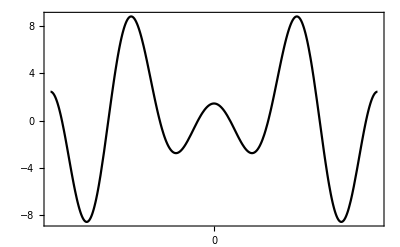

```mathematica
Plot[f[θ],{θ,-π,π},
Frame->True,
FrameTicks->{{Automatic,Automatic},{π/2 ints,Automatic}},PlotStyle->Black]
```

```mathematica
NullSpace[A†//N]
```

{{-0.0581001,-0.0723511,-0.0699159,-0.0661046,-0.0609932,351,-0.0207001,-0.0210178,-0.0212468,-0.0213851,-0.0214313},351,{1}}
 |  |  |  |

```mathematica
NullSpace[A//N]
```

{}

```mathematica
$tick;
NullSpace[A†]
tiempo["null space"];
```

{1}
 |  |  |  |

null space
CPU time: 6758.83 sec; 112.647 min; 1.87745 hr
elapsed time: 6767.860876 sec; 112.798 min; 1.87996 hr

## 2 automate

```mathematica
d=10;
vector=Cos[# θ]&/@Range[0,d]
```

{1,Cos[θ],Cos[2 θ],Cos[3 θ],Cos[4 θ],Cos[5 θ],Cos[6 θ],Cos[7 θ],Cos[8 θ],Cos[9 θ],Cos[10 θ]}

```mathematica
A=Table[
θ=(j-181)π/180;
vector
,{j,m}];
Dimensions[A]
Wx=Simplify[A†.A];
```

{361,11}

```mathematica
invWx=Inverse[Wx];
b=A†.σ;
```

$Aborted

```mathematica
c=InvWx.b
```

```mathematica
c=LeastSquares[A,σ]
```

{-0.011518,1.67507,-3.43434,-0.866356,5.36803,-1.27947,1.37878,-0.366491,0.185488,0.0664406,-0.110785}

```mathematica
Clear[f,θ];
f[θ_]=c.vector
```

-0.011518+1.67507 Cos[θ]-3.43434 Cos[2 θ]-0.866356 Cos[3 θ]+5.36803 Cos[4 θ]-1.27947 Cos[5 θ]+1.37878 Cos[6 θ]-0.366491 Cos[7 θ]+0.185488 Cos[8 θ]+0.0664406 Cos[9 θ]-0.110785 Cos[10 θ]

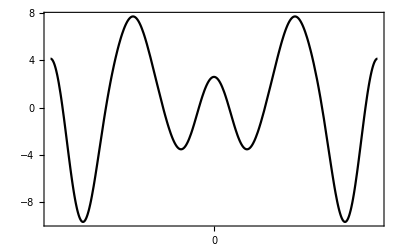

```mathematica
Plot[f[θ],{θ,-π,π},
Frame->True,
FrameTicks->{{Automatic,Automatic},{π/2 ints,Automatic}},PlotStyle->Black]
```

```mathematica
F=f[Table[
θ=(j-181)π/180,{j,m}]];
```

{4.14648,4.1201,4.04117,3.91024,3.72826,3.49654,3.21674,2.89091,2.52143,2.11101,1.6627,1.17984,0.666058,0.125262,-0.438416,-1.02063,-1.61686,-2.22243,-2.83257,-3.44243,-4.04717,-4.64192,-5.22192,-5.7825,-6.31915,-6.82758,-7.30373,-7.74385,-8.14453,-8.5027,-8.81572,-9.08137,-9.29789,-9.46397,-9.57881,-9.64207,-9.65389,-9.6149,-9.52616,-9.38916,-9.20582,-8.97839,-8.70947,-8.40194,-8.05891,-7.68368,-7.27969,-6.85046,-6.39955,-5.93049,-5.44678,-4.95179,-4.44873,-3.94067,-3.43044,-2.92065,-2.41365,-1.91154,-1.41613,-0.928985,-0.451402,0.0155753,0.47113,0.914659,1.34574,1.76412,2.16967,2.56235,2.9422,3.3093,3.66374,4.00558,4.33487,4.65158,4.95561,5.24678,5.52481,5.78932,6.03986,6.27586,6.49669,6.70165,6.89,7.06094,7.21371,7.3475,7.46159,7.55528,7.62796,7.67912,7.70834,7.71536,7.70003,7.66237,7.60255,7.52087,7.41782,7.29401,7.15019,6.98725,6.80618,6.60807,6.39408,6.16544,5.92342,5.66929,5.40434,5.12984,4.84703,4.5571,4.2612,3.96041,3.65572,3.34809,3.03837,2.72738,2.41584,2.10446,1.79387,1.48469,1.17753,0.872975,0.571629,0.274119,-0.0188981,-0.306719,-0.588591,-0.863702,-1.13118,-1.39008,-1.63942,-1.87814,-2.10515,-2.31931,-2.51947,-2.70445,-2.87311,-3.02432,-3.15701,-3.27017,-3.36289,-3.43435,-3.48388,-3.51095,-3.51519,-3.4964,-3.45458,-3.3899,-3.30274,-3.1937,-3.06352,-2.9132,-2.74386,-2.55684,-2.35361,-2.1358,-1.90515,-1.66352,-1.41285,-1.15515,-0.892457,-0.626851,-0.360405,-0.095179,0.166806,0.42358,0.673241,0.913968,1.14403,1.36182,1.56581,1.75461,1.92696,2.08173,2.21789,2.33459,2.43108,2.50675,2.56114,2.59391,2.60485,2.59391,2.56114,2.50675,2.43108,2.33459,2.21789,2.08173,1.92696,1.75461,1.56581,1.36182,1.14403,0.913968,0.673241,0.42358,0.166806,-0.095179,-0.360405,-0.626851,-0.892457,-1.15515,-1.41285,-1.66352,-1.90515,-2.1358,-2.35361,-2.55684,-2.74386,-2.9132,-3.06352,-3.1937,-3.30274,-3.3899,-3.45458,-3.4964,-3.51519,-3.51095,-3.48388,-3.43435,-3.36289,-3.27017,-3.15701,-3.02432,-2.87311,-2.70445,-2.51947,-2.31931,-2.10515,-1.87814,-1.63942,-1.39008,-1.13118,-0.863702,-0.588591,-0.306719,-0.0188981,0.274119,0.571629,0.872975,1.17753,1.48469,1.79387,2.10446,2.41584,2.72738,3.03837,3.34809,3.65572,3.96041,4.2612,4.5571,4.84703,5.12984,5.40434,5.66929,5.92342,6.16544,6.39408,6.60807,6.80618,6.98725,7.15019,7.29401,7.41782,7.52087,7.60255,7.66237,7.70003,7.71536,7.70834,7.67912,7.62796,7.55528,7.46159,7.3475,7.21371,7.06094,6.89,6.70165,6.49669,6.27586,6.03986,5.78932,5.52481,5.24678,4.95561,4.65158,4.33487,4.00558,3.66374,3.3093,2.9422,2.56235,2.16967,1.76412,1.34574,0.914659,0.47113,0.0155753,-0.451402,-0.928985,-1.41613,-1.91154,-2.41365,-2.92065,-3.43044,-3.94067,-4.44873,-4.95179,-5.44678,-5.93049,-6.39955,-6.85046,-7.27969,-7.68368,-8.05891,-8.40194,-8.70947,-8.97839,-9.20582,-9.38916,-9.52616,-9.6149,-9.65389,-9.64207,-9.57881,-9.46397,-9.29789,-9.08137,-8.81572,-8.5027,-8.14453,-7.74385,-7.30373,-6.82758,-6.31915,-5.7825,-5.22192,-4.64192,-4.04717,-3.44243,-2.83257,-2.22243,-1.61686,-1.02063,-0.438416,0.125262,0.666058,1.17984,1.6627,2.11101,2.52143,2.89091,3.21674,3.49654,3.72826,3.91024,4.04117,4.1201,4.14648}

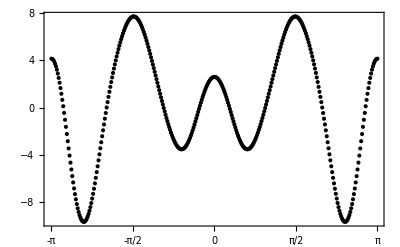

```mathematica
gf=ListPlot[F,
Frame->True,
FrameTicks->{{Automatic,Automatic},{{{1,-π},{91,-π/2},{181,0},{271,π/2},{361,π}},Automatic}},PlotStyle->Black]
```

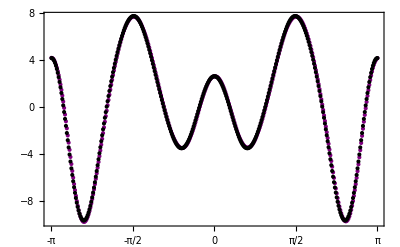

```mathematica
Show[{gσ,gf}]
```

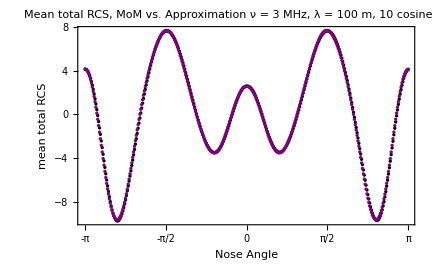

```mathematica
ListPlot[{σ,F},
Frame->True,
FrameTicks->{{Automatic,Automatic},{{{1,-π},{91,-π/2},{181,0},{271,π/2},{361,π}},Automatic}},PlotStyle->{Black,Purple},
PlotLabel->Style["Mean total RCS, MoM vs. Approximation"<>lf<>" ν = 3 MHz, λ = 100 m, 10 cosine terms",Bold],
FrameLabel->{"Nose Angle","mean total RCS"},
ImageSize->6 72]
```

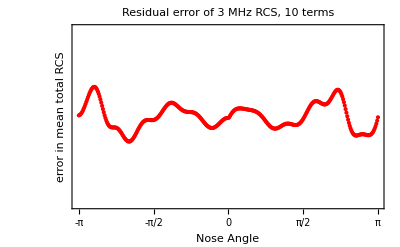

```mathematica
ListPlot[σ-F,
Frame->True,
FrameTicks->{{ints,Automatic},{{{1,-π},{91,-π/2},{181,0},{271,π/2},{361,π}},Automatic}},PlotStyle->Red,PlotRange->1.2{-1,1},
ImagePadding->{{Automatic,3},{Automatic,Automatic}},
PlotLabel->"Residual error of 3 MHz RCS, 10 terms",
FrameLabel->{"Nose Angle","error in mean total RCS"}]
```

## 3 correct linear system

```mathematica
𝓂=360;
```

```mathematica
A=Table[
θ=(j-180)π/180;
{1,Cos[θ],Cos[2θ],Cos[3θ],Cos[4θ],Cos[5θ],Cos[6θ],Cos[7θ]}
,{j,𝓂}];
```

Table::iterb: Iterator {j,𝓂} does not have appropriate bounds.

```mathematica
Dimensions[A]
```

{360,8}

```mathematica
Wx=Simplify[A†.A];
```

```mathematica
Dimensions[Wx]
```

{8,8}

```mathematica
FullSimplify[Wx]//mf
```

$Aborted

```mathematica
Wxx=FullSimplify[Wx];
%//mf
```

```mathematica
Wx//mf
```

(361 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-1 | 21+4 Cos[π/180]^2+4 Cos[π/90]^2+4 Cos[π/60]^2+4 Cos[π/45]^2+4 Cos[π/36]^2+4 Cos[π/30]^2+4 Cos[(7 π)/180]^2+4 Cos[(2 π)/45]^2+4 Cos[π/20]^2+4 Cos[π/18]^2+4 Cos[(11 π)/180]^2+4 Cos[π/15]^2+4 Cos[(13 π)/180]^2+4 Cos[(7 π)/90]^2+4 Cos[(4 π)/45]^2+4 Cos[(17 π)/180]^2+4 Cos[(19 π)/180]^2+4 Cos[π/9]^2+4 Cos[(7 π)/60]^2+4 Cos[(11 π)/90]^2+4 Cos[(23 π)/180]^2+4 Cos[(2 π)/15]^2+4 Cos[(5 π)/36]^2+4 Cos[(13 π)/90]^2+4 Cos[(3 π)/20]^2+4 Cos[(7 π)/45]^2+4 Cos[(29 π)/180]^2+4 Cos[(31 π)/180]^2+4 Cos[(8 π)/45]^2+4 Cos[(11 π)/60]^2+4 Cos[(17 π)/90]^2+4 Cos[(7 π)/36]^2+4 Cos[(37 π)/180]^2+4 Cos[(19 π)/90]^2+4 Cos[(13 π)/60]^2+4 Cos[(2 π)/9]^2+4 Cos[(41 π)/180]^2+4 Cos[(7 π)/30]^2+4 Cos[(43 π)/180]^2+4 Cos[(11 π)/45]^2+4 Sin[π/180]^2+4 Sin[π/90]^2+4 Sin[π/60]^2+4 Sin[π/45]^2+4 Sin[π/36]^2+4 Sin[π/30]^2+4 Sin[(7 π)/180]^2+4 Sin[(2 π)/45]^2+4 Sin[π/20]^2+4 Sin[π/18]^2+4 Sin[(11 π)/180]^2+4 Sin[π/15]^2+4 Sin[(13 π)/180]^2+4 Sin[(7 π)/90]^2+4 Sin[(4 π)/45]^2+4 Sin[(17 π)/180]^2+4 Sin[(19 π)/180]^2+4 Sin[π/9]^2+4 Sin[(7 π)/60]^2+4 Sin[(11 π)/90]^2+4 Sin[(23 π)/180]^2+4 Sin[(2 π)/15]^2+4 Sin[(5 π)/36]^2+4 Sin[(13 π)/90]^2+4 Sin[(3 π)/20]^2+4 Sin[(7 π)/45]^2+4 Sin[(29 π)/180]^2+4 Sin[(31 π)/180]^2+4 Sin[(8 π)/45]^2+4 Sin[(11 π)/60]^2+4 Sin[(17 π)/90]^2+4 Sin[(7 π)/36]^2+4 Sin[(37 π)/180]^2+4 Sin[(19 π)/90]^2+4 Sin[(13 π)/60]^2+4 Sin[(2 π)/9]^2+4 Sin[(41 π)/180]^2+4 Sin[(7 π)/30]^2+4 Sin[(43 π)/180]^2+4 Sin[(11 π)/45]^2 | -1 | -1+4 Cos[π/180] Cos[π/60]+(√2+√6) Cos[π/36]+√(2 (5+√5)) Cos[π/30]+4 Cos[π/90] Cos[π/30]+4 Cos[π/60] Cos[π/20]+2 √3 Cos[π/18]+Cos[π/15]+√5 Cos[π/15]+4 Cos[π/45] Cos[π/15]+2 Cos[π/9]+4 Cos[(7 π)/180] Cos[(7 π)/60]-Cos[(2 π)/15]+√5 Cos[(2 π)/15]+4 Cos[(2 π)/45] Cos[(2 π)/15]-√2 Cos[(5 π)/36]+√6 Cos[(5 π)/36]+4 Cos[π/20] Cos[(3 π)/20]+4 Cos[(11 π)/180] Cos[(11 π)/60]+√2 Cos[(7 π)/36]-√6 Cos[(7 π)/36]+4 Cos[(13 π)/180] Cos[(13 π)/60]-2 Cos[(2 π)/9]-√(10-2 √5) Cos[(7 π)/30]+4 Cos[(7 π)/90] Cos[(7 π)/30]+4 Cos[(29 π)/180] Sin[π/60]-4 Cos[(31 π)/180] Sin[π/60]-4 Sin[π/180] Sin[π/60]+√2 Sin[π/36]-√6 Sin[π/36]+Sin[π/30]-√5 Sin[π/30]+4 Cos[(7 π)/45] Sin[π/30]-4 Cos[(8 π)/45] Sin[π/30]-4 Sin[π/90] Sin[π/30]+4 Cos[(3 π)/20] Sin[π/20]-4 Cos[(11 π)/60] Sin[π/20]-4 Sin[π/60] Sin[π/20]-2 Sin[π/18]-√(10-2 √5) Sin[π/15]+4 Cos[(13 π)/90] Sin[π/15]-4 Cos[(17 π)/90] Sin[π/15]-4 Sin[π/45] Sin[π/15]-4 Cos[(7 π)/30] Sin[(4 π)/45]-4 Cos[(13 π)/60] Sin[(17 π)/180]-4 Cos[(11 π)/60] Sin[(19 π)/180]-2 √3 Sin[π/9]+4 Cos[(23 π)/180] Sin[(7 π)/60]-4 Cos[(3 π)/20] Sin[(7 π)/60]-4 Cos[(37 π)/180] Sin[(7 π)/60]-4 Sin[(7 π)/180] Sin[(7 π)/60]-4 Cos[(2 π)/15] Sin[(11 π)/90]-4 Cos[(7 π)/60] Sin[(23 π)/180]-√(2 (5+√5)) Sin[(2 π)/15]+4 Cos[(11 π)/90] Sin[(2 π)/15]-4 Cos[(19 π)/90] Sin[(2 π)/15]-4 Sin[(2 π)/45] Sin[(2 π)/15]-√2 Sin[(5 π)/36]-√6 Sin[(5 π)/36]-4 Cos[π/15] Sin[(13 π)/90]-4 Cos[π/20] Sin[(3 π)/20]+4 Cos[(7 π)/60] Sin[(3 π)/20]-4 Cos[(13 π)/60] Sin[(3 π)/20]-4 Sin[π/20] Sin[(3 π)/20]-4 Cos[π/30] Sin[(7 π)/45]-4 Cos[π/60] Sin[(29 π)/180]-4 Cos[π/60] Sin[(31 π)/180]-4 Cos[π/30] Sin[(8 π)/45]-4 Cos[π/20] Sin[(11 π)/60]+4 Cos[(19 π)/180] Sin[(11 π)/60]-4 Cos[(41 π)/180] Sin[(11 π)/60]-4 Sin[(11 π)/180] Sin[(11 π)/60]-4 Cos[π/15] Sin[(17 π)/90]-√2 Sin[(7 π)/36]-√6 Sin[(7 π)/36]-4 Cos[(7 π)/60] Sin[(37 π)/180]-4 Cos[(2 π)/15] Sin[(19 π)/90]+4 Cos[(17 π)/180] Sin[(13 π)/60]-4 Cos[(3 π)/20] Sin[(13 π)/60]-4 Cos[(43 π)/180] Sin[(13 π)/60]-4 Sin[(13 π)/180] Sin[(13 π)/60]-2 √3 Sin[(2 π)/9]-4 Cos[(11 π)/60] Sin[(41 π)/180]-Sin[(7 π)/30]-√5 Sin[(7 π)/30]+4 Cos[(4 π)/45] Sin[(7 π)/30]-4 Cos[(11 π)/45] Sin[(7 π)/30]-4 Sin[(7 π)/90] Sin[(7 π)/30]-4 Cos[(13 π)/60] Sin[(43 π)/180]-4 Cos[(7 π)/30] Sin[(11 π)/45] | -1 | -1+√2 (1+√3) Cos[π/60]+4 Cos[π/180] Cos[π/36]+2 √3 Cos[π/30]+2 √2 Cos[π/20]+4 Cos[π/90] Cos[π/18]+2 Cos[π/15]+4 Cos[π/45] Cos[π/9]-√2 (-1+√3) Cos[(7 π)/60]-2 Cos[(2 π)/15]+4 Cos[π/36] Cos[(5 π)/36]-2 √2 Cos[(3 π)/20]-4 Cos[(5 π)/36] Cos[(31 π)/180]-4 Cos[π/9] Cos[(8 π)/45]-√2 (1+√3) Cos[(11 π)/60]-4 Cos[π/18] Cos[(17 π)/90]-4 Cos[π/36] Cos[(7 π)/36]+4 Cos[(7 π)/180] Cos[(7 π)/36]-4 Cos[(29 π)/180] Cos[(7 π)/36]-4 Cos[π/36] Cos[(37 π)/180]-4 Cos[π/18] Cos[(19 π)/90]-√2 (1+√3) Cos[(13 π)/60]+4 Cos[(2 π)/45] Cos[(2 π)/9]-4 Cos[(7 π)/45] Cos[(2 π)/9]-4 Cos[(5 π)/36] Cos[(41 π)/180]-2 √3 Cos[(7 π)/30]-4 Cos[(7 π)/36] Cos[(43 π)/180]-4 Cos[(2 π)/9] Cos[(11 π)/45]-1/2 Csc[π/18]+1/2 Sec[π/9]+√2 (-1+√3) Sin[π/60]+4 Cos[(17 π)/180] Sin[π/36]-4 Cos[(19 π)/180] Sin[π/36]+4 Sin[π/180] Sin[π/36]+2 Sin[π/30]+2 √2 Sin[π/20]+4 Cos[(4 π)/45] Sin[π/18]-4 Cos[π/9] Sin[π/18]+4 Sin[π/90] Sin[π/18]+4 Cos[(7 π)/36] Sin[(11 π)/180]+2 √3 Sin[π/15]+4 Cos[(5 π)/36] Sin[(13 π)/180]+4 Cos[π/9] Sin[(7 π)/90]+4 Cos[π/18] Sin[(4 π)/45]+4 Cos[π/36] Sin[(17 π)/180]+4 Cos[π/36] Sin[(19 π)/180]+4 Cos[π/18] Sin[π/9]+4 Cos[(7 π)/90] Sin[π/9]-4 Cos[(11 π)/90] Sin[π/9]+4 Sin[π/45] Sin[π/9]+√2 (1+√3) Sin[(7 π)/60]+4 Cos[π/9] Sin[(11 π)/90]+4 Cos[(5 π)/36] Sin[(23 π)/180]+2 √3 Sin[(2 π)/15]+4 Cos[(13 π)/180] Sin[(5 π)/36]-4 Cos[(23 π)/180] Sin[(5 π)/36]+4 Cos[(7 π)/36] Sin[(5 π)/36]+4 Sin[π/36] Sin[(5 π)/36]+4 Cos[(2 π)/9] Sin[(13 π)/90]+2 √2 Sin[(3 π)/20]+4 Sin[(5 π)/36] Sin[(31 π)/180]+4 Sin[π/9] Sin[(8 π)/45]+√2 (-1+√3) Sin[(11 π)/60]+4 Sin[π/18] Sin[(17 π)/90]+4 Cos[(11 π)/180] Sin[(7 π)/36]-4 Cos[(5 π)/36] Sin[(7 π)/36]+4 Sin[π/36] Sin[(7 π)/36]+4 Sin[(7 π)/180] Sin[(7 π)/36]+4 Sin[(29 π)/180] Sin[(7 π)/36]-4 Sin[π/36] Sin[(37 π)/180]-4 Sin[π/18] Sin[(19 π)/90]-√2 (-1+√3) Sin[(13 π)/60]+4 Cos[π/18] Sin[(2 π)/9]-4 Cos[(13 π)/90] Sin[(2 π)/9]+4 Sin[(2 π)/45] Sin[(2 π)/9]-4 Sin[π/9] Sin[(2 π)/9]+4 Sin[(7 π)/45] Sin[(2 π)/9]-4 Sin[(5 π)/36] Sin[(41 π)/180]-2 Sin[(7 π)/30]-4 Sin[(7 π)/36] Sin[(43 π)/180]-4 Sin[(2 π)/9] Sin[(11 π)/45] | -1 | 1/2 (-2+8 Cos[π/60] Cos[(7 π)/60]-8 Cos[(19 π)/180] Cos[(23 π)/180]-8 Cos[π/15] Cos[(2 π)/15]-8 Cos[π/36] Cos[(5 π)/36]+8 Cos[π/90] (Cos[(7 π)/90]-Cos[(13 π)/90])-8 Cos[(11 π)/90] Cos[(13 π)/90]-8 Cos[π/20] Cos[(3 π)/20]+8 Cos[π/45] Cos[(7 π)/45]-8 Cos[(4 π)/45] Cos[(7 π)/45]-8 Cos[(23 π)/180] Cos[(29 π)/180]-8 Cos[(7 π)/60] Cos[(11 π)/60]+8 Cos[π/36] Cos[(7 π)/36]-8 Cos[(31 π)/180] Cos[(37 π)/180]+8 Cos[π/30] Cos[(7 π)/30]-8 Cos[(8 π)/45] Cos[(11 π)/45]-Csc[π/18]+Sec[π/9]-8 Cos[(13 π)/180] Sin[π/180]+8 Cos[(13 π)/60] Sin[π/60]-8 Cos[(19 π)/90] Sin[π/45]+8 Cos[π/15] Sin[π/30]-8 Cos[(41 π)/180] Sin[(7 π)/180]-8 Sin[π/180] Sin[(7 π)/180]-8 Cos[(7 π)/90] Sin[(2 π)/45]-8 Cos[(17 π)/90] Sin[(2 π)/45]-8 Cos[(3 π)/20] Sin[π/20]-8 Cos[π/9] Sin[π/18]-8 Cos[(13 π)/180] Sin[(11 π)/180]-8 Cos[(37 π)/180] Sin[(11 π)/180]-8 Cos[π/30] Sin[π/15]+8 Cos[π/180] (Cos[(7 π)/180]-Sin[(13 π)/180])+8 Cos[(11 π)/180] Sin[(13 π)/180]-8 Cos[(2 π)/45] Sin[(7 π)/90]-8 Sin[π/90] Sin[(7 π)/90]-8 Cos[(11 π)/90] Sin[(4 π)/45]-8 Cos[(29 π)/180] Sin[(17 π)/180]+8 Cos[(41 π)/180] Sin[(17 π)/180]-8 Cos[(43 π)/180] Sin[(19 π)/180]+8 Cos[π/18] Sin[π/9]-8 Sin[π/60] Sin[(7 π)/60]-8 Cos[(4 π)/45] Sin[(11 π)/90]-8 Sin[(19 π)/180] Sin[(23 π)/180]+8 Cos[(7 π)/30] Sin[(2 π)/15]-8 Sin[π/15] Sin[(2 π)/15]-8 Cos[(7 π)/36] Sin[(5 π)/36]-8 Sin[π/36] Sin[(5 π)/36]+8 Sin[π/90] Sin[(13 π)/90]-8 Sin[(11 π)/90] Sin[(13 π)/90]+8 Cos[π/20] Sin[(3 π)/20]+8 Sin[π/20] Sin[(3 π)/20]-8 Sin[π/45] Sin[(7 π)/45]+8 Sin[(4 π)/45] Sin[(7 π)/45]-8 Cos[(17 π)/180] Sin[(29 π)/180]+8 Sin[(23 π)/180] Sin[(29 π)/180]+8 Cos[(43 π)/180] Sin[(31 π)/180]-8 Cos[(17 π)/90] Sin[(8 π)/45]+8 Cos[(13 π)/60] Sin[(11 π)/60]-8 Sin[(7 π)/60] Sin[(11 π)/60]+8 Cos[(2 π)/45] Sin[(17 π)/90]+8 Cos[(8 π)/45] Sin[(17 π)/90]+8 Cos[(5 π)/36] Sin[(7 π)/36]-8 Sin[π/36] Sin[(7 π)/36]+8 Cos[(11 π)/180] Sin[(37 π)/180]+8 Sin[(31 π)/180] Sin[(37 π)/180]+8 Cos[π/45] Sin[(19 π)/90]+8 Cos[(11 π)/45] Sin[(19 π)/90]+8 Cos[π/60] Sin[(13 π)/60]-8 Cos[(11 π)/60] Sin[(13 π)/60]+8 Cos[π/18] Sin[(2 π)/9]-8 Sin[π/9] Sin[(2 π)/9]+8 Cos[(7 π)/180] Sin[(41 π)/180]+8 Cos[(17 π)/180] Sin[(41 π)/180]+8 Cos[(2 π)/15] Sin[(7 π)/30]-8 Sin[π/30] Sin[(7 π)/30]-8 Cos[(19 π)/180] Sin[(43 π)/180]+8 Cos[(31 π)/180] Sin[(43 π)/180]+8 Cos[(19 π)/90] Sin[(11 π)/45]+8 Sin[(8 π)/45] Sin[(11 π)/45])
1 | -1 | 181 | -1 | 1 | -1 | -3-8 Cos[π/45]+8 Cos[(2 π)/45]+4 √3 Cos[π/18]+2 Cos[π/15]+2 √5 Cos[π/15]+8 Cos[(4 π)/45]+4 Cos[π/9]-2 Cos[(2 π)/15]+2 √5 Cos[(2 π)/15]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]-4 Cos[(2 π)/9]-2 √(10-2 √5) Cos[(7 π)/30]-8 Cos[(11 π)/45]+8 Sin[π/90]+2 Sin[π/30]-2 √5 Sin[π/30]-4 Sin[π/18]-2 √(10-2 √5) Sin[π/15]-8 Sin[(7 π)/90]-4 √3 Sin[π/9]-8 Sin[(11 π)/90]+2 √(2 (5+√5)) (Cos[π/30]-Sin[(2 π)/15])+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]-8 Sin[(19 π)/90]-4 √3 Sin[(2 π)/9]-2 Sin[(7 π)/30]-2 √5 Sin[(7 π)/30] | -1
-1 | -1+4 Cos[π/180] Cos[π/60]+(√2+√6) Cos[π/36]+√(2 (5+√5)) Cos[π/30]+4 Cos[π/90] Cos[π/30]+4 Cos[π/60] Cos[π/20]+2 √3 Cos[π/18]+Cos[π/15]+√5 Cos[π/15]+4 Cos[π/45] Cos[π/15]+2 Cos[π/9]+4 Cos[(7 π)/180] Cos[(7 π)/60]-Cos[(2 π)/15]+√5 Cos[(2 π)/15]+4 Cos[(2 π)/45] Cos[(2 π)/15]-√2 Cos[(5 π)/36]+√6 Cos[(5 π)/36]+4 Cos[π/20] Cos[(3 π)/20]+4 Cos[(11 π)/180] Cos[(11 π)/60]+√2 Cos[(7 π)/36]-√6 Cos[(7 π)/36]+4 Cos[(13 π)/180] Cos[(13 π)/60]-2 Cos[(2 π)/9]-√(10-2 √5) Cos[(7 π)/30]+4 Cos[(7 π)/90] Cos[(7 π)/30]+4 Cos[(29 π)/180] Sin[π/60]-4 Cos[(31 π)/180] Sin[π/60]-4 Sin[π/180] Sin[π/60]+√2 Sin[π/36]-√6 Sin[π/36]+Sin[π/30]-√5 Sin[π/30]+4 Cos[(7 π)/45] Sin[π/30]-4 Cos[(8 π)/45] Sin[π/30]-4 Sin[π/90] Sin[π/30]+4 Cos[(3 π)/20] Sin[π/20]-4 Cos[(11 π)/60] Sin[π/20]-4 Sin[π/60] Sin[π/20]-2 Sin[π/18]-√(10-2 √5) Sin[π/15]+4 Cos[(13 π)/90] Sin[π/15]-4 Cos[(17 π)/90] Sin[π/15]-4 Sin[π/45] Sin[π/15]-4 Cos[(7 π)/30] Sin[(4 π)/45]-4 Cos[(13 π)/60] Sin[(17 π)/180]-4 Cos[(11 π)/60] Sin[(19 π)/180]-2 √3 Sin[π/9]+4 Cos[(23 π)/180] Sin[(7 π)/60]-4 Cos[(3 π)/20] Sin[(7 π)/60]-4 Cos[(37 π)/180] Sin[(7 π)/60]-4 Sin[(7 π)/180] Sin[(7 π)/60]-4 Cos[(2 π)/15] Sin[(11 π)/90]-4 Cos[(7 π)/60] Sin[(23 π)/180]-√(2 (5+√5)) Sin[(2 π)/15]+4 Cos[(11 π)/90] Sin[(2 π)/15]-4 Cos[(19 π)/90] Sin[(2 π)/15]-4 Sin[(2 π)/45] Sin[(2 π)/15]-√2 Sin[(5 π)/36]-√6 Sin[(5 π)/36]-4 Cos[π/15] Sin[(13 π)/90]-4 Cos[π/20] Sin[(3 π)/20]+4 Cos[(7 π)/60] Sin[(3 π)/20]-4 Cos[(13 π)/60] Sin[(3 π)/20]-4 Sin[π/20] Sin[(3 π)/20]-4 Cos[π/30] Sin[(7 π)/45]-4 Cos[π/60] Sin[(29 π)/180]-4 Cos[π/60] Sin[(31 π)/180]-4 Cos[π/30] Sin[(8 π)/45]-4 Cos[π/20] Sin[(11 π)/60]+4 Cos[(19 π)/180] Sin[(11 π)/60]-4 Cos[(41 π)/180] Sin[(11 π)/60]-4 Sin[(11 π)/180] Sin[(11 π)/60]-4 Cos[π/15] Sin[(17 π)/90]-√2 Sin[(7 π)/36]-√6 Sin[(7 π)/36]-4 Cos[(7 π)/60] Sin[(37 π)/180]-4 Cos[(2 π)/15] Sin[(19 π)/90]+4 Cos[(17 π)/180] Sin[(13 π)/60]-4 Cos[(3 π)/20] Sin[(13 π)/60]-4 Cos[(43 π)/180] Sin[(13 π)/60]-4 Sin[(13 π)/180] Sin[(13 π)/60]-2 √3 Sin[(2 π)/9]-4 Cos[(11 π)/60] Sin[(41 π)/180]-Sin[(7 π)/30]-√5 Sin[(7 π)/30]+4 Cos[(4 π)/45] Sin[(7 π)/30]-4 Cos[(11 π)/45] Sin[(7 π)/30]-4 Sin[(7 π)/90] Sin[(7 π)/30]-4 Cos[(13 π)/60] Sin[(43 π)/180]-4 Cos[(7 π)/30] Sin[(11 π)/45] | -1 | 181 | -1 | 1-8 Cos[π/45]+√2 (-1+√3) Cos[π/36]+8 Cos[(2 π)/45]-2 √3 Cos[π/18]+8 Cos[(4 π)/45]+2 Cos[π/9]+√2 Cos[(5 π)/36]+√6 Cos[(5 π)/36]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]-√2 Cos[(7 π)/36]-√6 Cos[(7 π)/36]-2 Cos[(2 π)/9]-8 Cos[(11 π)/45]+8 Sin[π/90]-√2 Sin[π/36]-√6 Sin[π/36]-2 Sin[π/18]-8 Sin[(7 π)/90]+2 √3 Sin[π/9]-8 Sin[(11 π)/90]+√2 Sin[(5 π)/36]-√6 Sin[(5 π)/36]+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]+√2 Sin[(7 π)/36]-√6 Sin[(7 π)/36]-8 Sin[(19 π)/90]+2 √3 Sin[(2 π)/9] | -1 | 1+(√2-√6) Cos[π/36]+4 Cos[π/60] Cos[(7 π)/180]-2 √3 Cos[π/18]+Cos[π/15]-√5 Cos[π/15]+4 Cos[π/30] Cos[(7 π)/90]+4 Cos[π/20] Cos[(7 π)/60]-4 Cos[(11 π)/180] Cos[(7 π)/60]-Cos[(2 π)/15]-√5 Cos[(2 π)/15]-√2 Cos[(5 π)/36]-√6 Cos[(5 π)/36]-4 Cos[π/60] Cos[(3 π)/20]-2 Cos[(7 π)/45]+4 Cos[π/15] Cos[(7 π)/45]-4 Cos[π/15] Cos[(8 π)/45]-4 Cos[(17 π)/180] Cos[(11 π)/60]+√2 Cos[(7 π)/36]+√6 Cos[(7 π)/36]-4 Cos[π/20] Cos[(13 π)/60]+4 Cos[(29 π)/180] Cos[(13 π)/60]-4 Cos[(31 π)/180] Cos[(13 π)/60]-2 Cos[(2 π)/9]+√(2 (5+√5)) Cos[(7 π)/30]+4 Cos[(11 π)/90] Cos[(7 π)/30]-4 Cos[(19 π)/90] Cos[(7 π)/30]+4 Cos[(11 π)/60] Cos[(43 π)/180]-4 Cos[(13 π)/60] Sin[π/180]-4 Cos[π/15] Sin[π/90]-4 Cos[(23 π)/180] Sin[π/60]+4 Cos[(37 π)/180] Sin[π/60]+√2 Sin[π/36]+√6 Sin[π/36]+Sin[π/30]+√5 Sin[π/30]-4 Cos[(4 π)/45] Sin[π/30]+4 Cos[(11 π)/45] Sin[π/30]+4 Sin[π/60] Sin[(7 π)/180]-4 Cos[(7 π)/30] Sin[(2 π)/45]-2 Sin[π/18]+√(2 (5+√5)) Sin[π/15]-4 Cos[π/90] Sin[π/15]+4 Cos[(11 π)/60] Sin[(13 π)/180]+4 Sin[π/30] Sin[(7 π)/90]-4 Cos[π/30] Sin[(4 π)/45]+4 Cos[(7 π)/60] Sin[(19 π)/180]+2 √3 Sin[π/9]-4 Cos[(19 π)/180] Sin[(7 π)/60]+4 Cos[(41 π)/180] Sin[(7 π)/60]+4 Sin[π/20] Sin[(7 π)/60]+4 Sin[(11 π)/180] Sin[(7 π)/60]-4 Cos[π/60] Sin[(23 π)/180]+√(10-2 √5) (Cos[π/30]-Sin[(2 π)/15])-4 Cos[(13 π)/90] Sin[(2 π)/15]+4 Cos[(17 π)/90] Sin[(2 π)/15]+4 Sin[π/45] Sin[(2 π)/15]-√2 Sin[(5 π)/36]+√6 Sin[(5 π)/36]+4 Cos[(2 π)/15] Sin[(13 π)/90]-4 Cos[(11 π)/60] Sin[(3 π)/20]-4 Sin[π/60] Sin[(3 π)/20]+4 Sin[π/15] Sin[(7 π)/45]+4 Sin[π/15] Sin[(8 π)/45]+4 Cos[(13 π)/180] Sin[(11 π)/60]+4 Cos[(3 π)/20] Sin[(11 π)/60]-4 Sin[(17 π)/180] Sin[(11 π)/60]+4 Cos[(2 π)/15] Sin[(17 π)/90]-√2 Sin[(7 π)/36]+√6 Sin[(7 π)/36]-4 Cos[π/60] Sin[(37 π)/180]+4 Cos[π/180] Sin[(13 π)/60]+4 Sin[π/20] Sin[(13 π)/60]-4 Sin[(29 π)/180] Sin[(13 π)/60]-4 Sin[(31 π)/180] Sin[(13 π)/60]+2 √3 Sin[(2 π)/9]+4 Cos[(7 π)/60] Sin[(41 π)/180]-Sin[(7 π)/30]+√5 Sin[(7 π)/30]+4 Cos[(2 π)/45] Sin[(7 π)/30]-4 Sin[(11 π)/90] Sin[(7 π)/30]-4 Sin[(19 π)/90] Sin[(7 π)/30]-4 Sin[(11 π)/60] Sin[(43 π)/180]-4 Cos[π/30] Sin[(11 π)/45]
1 | -1 | 1 | -1 | 177-8 Cos[π/45]+8 Cos[(2 π)/45]-8 Cos[π/15]+8 Cos[(4 π)/45]-8 Cos[π/9]+8 Cos[(2 π)/15]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]+8 Cos[(2 π)/9]-8 Cos[(11 π)/45]+8 Sin[π/90]-8 Sin[π/30]+8 Sin[π/18]-8 Sin[(7 π)/90]-8 Sin[(11 π)/90]+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]-8 Sin[(19 π)/90]+8 Sin[(7 π)/30] | -1 | 1 | -1
-1 | -1+√2 (1+√3) Cos[π/60]+4 Cos[π/180] Cos[π/36]+2 √3 Cos[π/30]+2 √2 Cos[π/20]+4 Cos[π/90] Cos[π/18]+2 Cos[π/15]+4 Cos[π/45] Cos[π/9]-√2 (-1+√3) Cos[(7 π)/60]-2 Cos[(2 π)/15]+4 Cos[π/36] Cos[(5 π)/36]-2 √2 Cos[(3 π)/20]-4 Cos[(5 π)/36] Cos[(31 π)/180]-4 Cos[π/9] Cos[(8 π)/45]-√2 (1+√3) Cos[(11 π)/60]-4 Cos[π/18] Cos[(17 π)/90]-4 Cos[π/36] Cos[(7 π)/36]+4 Cos[(7 π)/180] Cos[(7 π)/36]-4 Cos[(29 π)/180] Cos[(7 π)/36]-4 Cos[π/36] Cos[(37 π)/180]-4 Cos[π/18] Cos[(19 π)/90]-√2 (1+√3) Cos[(13 π)/60]+4 Cos[(2 π)/45] Cos[(2 π)/9]-4 Cos[(7 π)/45] Cos[(2 π)/9]-4 Cos[(5 π)/36] Cos[(41 π)/180]-2 √3 Cos[(7 π)/30]-4 Cos[(7 π)/36] Cos[(43 π)/180]-4 Cos[(2 π)/9] Cos[(11 π)/45]-1/2 Csc[π/18]+1/2 Sec[π/9]+√2 (-1+√3) Sin[π/60]+4 Cos[(17 π)/180] Sin[π/36]-4 Cos[(19 π)/180] Sin[π/36]+4 Sin[π/180] Sin[π/36]+2 Sin[π/30]+2 √2 Sin[π/20]+4 Cos[(4 π)/45] Sin[π/18]-4 Cos[π/9] Sin[π/18]+4 Sin[π/90] Sin[π/18]+4 Cos[(7 π)/36] Sin[(11 π)/180]+2 √3 Sin[π/15]+4 Cos[(5 π)/36] Sin[(13 π)/180]+4 Cos[π/9] Sin[(7 π)/90]+4 Cos[π/18] Sin[(4 π)/45]+4 Cos[π/36] Sin[(17 π)/180]+4 Cos[π/36] Sin[(19 π)/180]+4 Cos[π/18] Sin[π/9]+4 Cos[(7 π)/90] Sin[π/9]-4 Cos[(11 π)/90] Sin[π/9]+4 Sin[π/45] Sin[π/9]+√2 (1+√3) Sin[(7 π)/60]+4 Cos[π/9] Sin[(11 π)/90]+4 Cos[(5 π)/36] Sin[(23 π)/180]+2 √3 Sin[(2 π)/15]+4 Cos[(13 π)/180] Sin[(5 π)/36]-4 Cos[(23 π)/180] Sin[(5 π)/36]+4 Cos[(7 π)/36] Sin[(5 π)/36]+4 Sin[π/36] Sin[(5 π)/36]+4 Cos[(2 π)/9] Sin[(13 π)/90]+2 √2 Sin[(3 π)/20]+4 Sin[(5 π)/36] Sin[(31 π)/180]+4 Sin[π/9] Sin[(8 π)/45]+√2 (-1+√3) Sin[(11 π)/60]+4 Sin[π/18] Sin[(17 π)/90]+4 Cos[(11 π)/180] Sin[(7 π)/36]-4 Cos[(5 π)/36] Sin[(7 π)/36]+4 Sin[π/36] Sin[(7 π)/36]+4 Sin[(7 π)/180] Sin[(7 π)/36]+4 Sin[(29 π)/180] Sin[(7 π)/36]-4 Sin[π/36] Sin[(37 π)/180]-4 Sin[π/18] Sin[(19 π)/90]-√2 (-1+√3) Sin[(13 π)/60]+4 Cos[π/18] Sin[(2 π)/9]-4 Cos[(13 π)/90] Sin[(2 π)/9]+4 Sin[(2 π)/45] Sin[(2 π)/9]-4 Sin[π/9] Sin[(2 π)/9]+4 Sin[(7 π)/45] Sin[(2 π)/9]-4 Sin[(5 π)/36] Sin[(41 π)/180]-2 Sin[(7 π)/30]-4 Sin[(7 π)/36] Sin[(43 π)/180]-4 Sin[(2 π)/9] Sin[(11 π)/45] | -1 | 1-8 Cos[π/45]+√2 (-1+√3) Cos[π/36]+8 Cos[(2 π)/45]-2 √3 Cos[π/18]+8 Cos[(4 π)/45]+2 Cos[π/9]+√2 Cos[(5 π)/36]+√6 Cos[(5 π)/36]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]-√2 Cos[(7 π)/36]-√6 Cos[(7 π)/36]-2 Cos[(2 π)/9]-8 Cos[(11 π)/45]+8 Sin[π/90]-√2 Sin[π/36]-√6 Sin[π/36]-2 Sin[π/18]-8 Sin[(7 π)/90]+2 √3 Sin[π/9]-8 Sin[(11 π)/90]+√2 Sin[(5 π)/36]-√6 Sin[(5 π)/36]+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]+√2 Sin[(7 π)/36]-√6 Sin[(7 π)/36]-8 Sin[(19 π)/90]+2 √3 Sin[(2 π)/9] | -1 | 181 | -1 | 1-√2 (-1+√3) Cos[π/60]-2 √3 Cos[π/30]+4 Cos[π/36] Cos[(7 π)/180]+2 √2 Cos[π/20]+2 Cos[π/15]+4 Cos[π/18] Cos[(7 π)/90]-4 Cos[(2 π)/45] Cos[π/9]+√2 (1+√3) Cos[(7 π)/60]-4 Cos[π/18] Cos[(11 π)/90]-2 Cos[(2 π)/15]-4 Cos[π/180] Cos[(5 π)/36]-2 √2 Cos[(3 π)/20]+4 Cos[π/9] Cos[(7 π)/45]-4 Cos[π/36] Cos[(29 π)/180]+√2 (-1+√3) Cos[(11 π)/60]-4 Cos[(13 π)/180] Cos[(7 π)/36]+4 Cos[(23 π)/180] Cos[(7 π)/36]+4 Cos[(5 π)/36] Cos[(7 π)/36]+4 Cos[(5 π)/36] Cos[(37 π)/180]+√2 (-1+√3) Cos[(13 π)/60]+4 Cos[(4 π)/45] Cos[(2 π)/9]+2 √3 Cos[(7 π)/30]-4 Cos[π/36] Cos[(43 π)/180]+4 Cos[π/9] Cos[(11 π)/45]-1/2 Csc[π/18]+1/2 Sec[π/9]+4 Cos[(2 π)/9] Sin[π/90]-√2 (1+√3) Sin[π/60]+4 Cos[π/18] Sin[π/45]-4 Cos[(11 π)/180] Sin[π/36]+4 Cos[(5 π)/36] Sin[π/36]-4 Cos[(7 π)/36] Sin[π/36]+2 Sin[π/30]-4 Sin[π/36] Sin[(7 π)/180]+2 √2 Sin[π/20]-4 Cos[π/45] Sin[π/18]-4 Cos[π/9] Sin[π/18]+4 Cos[(8 π)/45] Sin[π/18]+4 Cos[π/36] Sin[(11 π)/180]-2 √3 Sin[π/15]-4 Sin[π/18] Sin[(7 π)/90]-4 Cos[(5 π)/36] Sin[(17 π)/180]-4 Cos[(5 π)/36] Sin[(19 π)/180]+2 Sin[π/9]-4 Cos[π/18] Sin[π/9]+4 Cos[(13 π)/90] Sin[π/9]-4 Sin[(2 π)/45] Sin[π/9]-√2 (-1+√3) Sin[(7 π)/60]-4 Sin[π/18] Sin[(11 π)/90]-2 √3 Sin[(2 π)/15]-4 Cos[(17 π)/180] Sin[(5 π)/36]+4 Cos[(19 π)/180] Sin[(5 π)/36]-4 Sin[π/180] Sin[(5 π)/36]-4 Cos[π/9] Sin[(13 π)/90]+2 √2 Sin[(3 π)/20]-4 Sin[π/9] Sin[(7 π)/45]-4 Sin[π/36] Sin[(29 π)/180]-4 Cos[(7 π)/36] Sin[(31 π)/180]+4 Cos[π/18] Sin[(8 π)/45]-√2 (1+√3) Sin[(11 π)/60]+4 Cos[(2 π)/9] Sin[(17 π)/90]-4 Cos[(31 π)/180] Sin[(7 π)/36]-4 Cos[(41 π)/180] Sin[(7 π)/36]+4 Sin[(13 π)/180] Sin[(7 π)/36]+4 Sin[(23 π)/180] Sin[(7 π)/36]-4 Sin[(5 π)/36] Sin[(7 π)/36]+4 Sin[(5 π)/36] Sin[(37 π)/180]-4 Cos[(2 π)/9] Sin[(19 π)/90]+√2 (1+√3) Sin[(13 π)/60]+2 Sin[(2 π)/9]+4 Cos[π/90] Sin[(2 π)/9]-4 Cos[π/18] Sin[(2 π)/9]-4 Cos[(17 π)/90] Sin[(2 π)/9]-4 Cos[(19 π)/90] Sin[(2 π)/9]+4 Sin[(4 π)/45] Sin[(2 π)/9]+4 Sin[π/9] Sin[(2 π)/9]+4 Cos[(7 π)/36] Sin[(41 π)/180]-2 Sin[(7 π)/30]+4 Sin[π/36] Sin[(43 π)/180]+4 Sin[π/9] Sin[(11 π)/45]
1 | -1 | -3-8 Cos[π/45]+8 Cos[(2 π)/45]+4 √3 Cos[π/18]+2 Cos[π/15]+2 √5 Cos[π/15]+8 Cos[(4 π)/45]+4 Cos[π/9]-2 Cos[(2 π)/15]+2 √5 Cos[(2 π)/15]-8 Cos[(7 π)/45]+8 Cos[(8 π)/45]-4 Cos[(2 π)/9]-2 √(10-2 √5) Cos[(7 π)/30]-8 Cos[(11 π)/45]+8 Sin[π/90]+2 Sin[π/30]-2 √5 Sin[π/30]-4 Sin[π/18]-2 √(10-2 √5) Sin[π/15]-8 Sin[(7 π)/90]-4 √3 Sin[π/9]-8 Sin[(11 π)/90]+2 √(2 (5+√5)) (Cos[π/30]-Sin[(2 π)/15])+8 Sin[(13 π)/90]+8 Sin[(17 π)/90]-8 Sin[(19 π)/90]-4 √3 Sin[(2 π)/9]-2 Sin[(7 π)/30]-2 √5 Sin[(7 π)/30] | -1 | 1 | -1 | 181 | -1
-1 | 1/2 (-2+8 Cos[π/60] Cos[(7 π)/60]-8 Cos[(19 π)/180] Cos[(23 π)/180]-8 Cos[π/15] Cos[(2 π)/15]-8 Cos[π/36] Cos[(5 π)/36]+8 Cos[π/90] (Cos[(7 π)/90]-Cos[(13 π)/90])-8 Cos[(11 π)/90] Cos[(13 π)/90]-8 Cos[π/20] Cos[(3 π)/20]+8 Cos[π/45] Cos[(7 π)/45]-8 Cos[(4 π)/45] Cos[(7 π)/45]-8 Cos[(23 π)/180] Cos[(29 π)/180]-8 Cos[(7 π)/60] Cos[(11 π)/60]+8 Cos[π/36] Cos[(7 π)/36]-8 Cos[(31 π)/180] Cos[(37 π)/180]+8 Cos[π/30] Cos[(7 π)/30]-8 Cos[(8 π)/45] Cos[(11 π)/45]-Csc[π/18]+Sec[π/9]-8 Cos[(13 π)/180] Sin[π/180]+8 Cos[(13 π)/60] Sin[π/60]-8 Cos[(19 π)/90] Sin[π/45]+8 Cos[π/15] Sin[π/30]-8 Cos[(41 π)/180] Sin[(7 π)/180]-8 Sin[π/180] Sin[(7 π)/180]-8 Cos[(7 π)/90] Sin[(2 π)/45]-8 Cos[(17 π)/90] Sin[(2 π)/45]-8 Cos[(3 π)/20] Sin[π/20]-8 Cos[π/9] Sin[π/18]-8 Cos[(13 π)/180] Sin[(11 π)/180]-8 Cos[(37 π)/180] Sin[(11 π)/180]-8 Cos[π/30] Sin[π/15]+8 Cos[π/180] (Cos[(7 π)/180]-Sin[(13 π)/180])+8 Cos[(11 π)/180] Sin[(13 π)/180]-8 Cos[(2 π)/45] Sin[(7 π)/90]-8 Sin[π/90] Sin[(7 π)/90]-8 Cos[(11 π)/90] Sin[(4 π)/45]-8 Cos[(29 π)/180] Sin[(17 π)/180]+8 Cos[(41 π)/180] Sin[(17 π)/180]-8 Cos[(43 π)/180] Sin[(19 π)/180]+8 Cos[π/18] Sin[π/9]-8 Sin[π/60] Sin[(7 π)/60]-8 Cos[(4 π)/45] Sin[(11 π)/90]-8 Sin[(19 π)/180] Sin[(23 π)/180]+8 Cos[(7 π)/30] Sin[(2 π)/15]-8 Sin[π/15] Sin[(2 π)/15]-8 Cos[(7 π)/36] Sin[(5 π)/36]-8 Sin[π/36] Sin[(5 π)/36]+8 Sin[π/90] Sin[(13 π)/90]-8 Sin[(11 π)/90] Sin[(13 π)/90]+8 Cos[π/20] Sin[(3 π)/20]+8 Sin[π/20] Sin[(3 π)/20]-8 Sin[π/45] Sin[(7 π)/45]+8 Sin[(4 π)/45] Sin[(7 π)/45]-8 Cos[(17 π)/180] Sin[(29 π)/180]+8 Sin[(23 π)/180] Sin[(29 π)/180]+8 Cos[(43 π)/180] Sin[(31 π)/180]-8 Cos[(17 π)/90] Sin[(8 π)/45]+8 Cos[(13 π)/60] Sin[(11 π)/60]-8 Sin[(7 π)/60] Sin[(11 π)/60]+8 Cos[(2 π)/45] Sin[(17 π)/90]+8 Cos[(8 π)/45] Sin[(17 π)/90]+8 Cos[(5 π)/36] Sin[(7 π)/36]-8 Sin[π/36] Sin[(7 π)/36]+8 Cos[(11 π)/180] Sin[(37 π)/180]+8 Sin[(31 π)/180] Sin[(37 π)/180]+8 Cos[π/45] Sin[(19 π)/90]+8 Cos[(11 π)/45] Sin[(19 π)/90]+8 Cos[π/60] Sin[(13 π)/60]-8 Cos[(11 π)/60] Sin[(13 π)/60]+8 Cos[π/18] Sin[(2 π)/9]-8 Sin[π/9] Sin[(2 π)/9]+8 Cos[(7 π)/180] Sin[(41 π)/180]+8 Cos[(17 π)/180] Sin[(41 π)/180]+8 Cos[(2 π)/15] Sin[(7 π)/30]-8 Sin[π/30] Sin[(7 π)/30]-8 Cos[(19 π)/180] Sin[(43 π)/180]+8 Cos[(31 π)/180] Sin[(43 π)/180]+8 Cos[(19 π)/90] Sin[(11 π)/45]+8 Sin[(8 π)/45] Sin[(11 π)/45]) | -1 | 1+(√2-√6) Cos[π/36]+4 Cos[π/60] Cos[(7 π)/180]-2 √3 Cos[π/18]+Cos[π/15]-√5 Cos[π/15]+4 Cos[π/30] Cos[(7 π)/90]+4 Cos[π/20] Cos[(7 π)/60]-4 Cos[(11 π)/180] Cos[(7 π)/60]-Cos[(2 π)/15]-√5 Cos[(2 π)/15]-√2 Cos[(5 π)/36]-√6 Cos[(5 π)/36]-4 Cos[π/60] Cos[(3 π)/20]-2 Cos[(7 π)/45]+4 Cos[π/15] Cos[(7 π)/45]-4 Cos[π/15] Cos[(8 π)/45]-4 Cos[(17 π)/180] Cos[(11 π)/60]+√2 Cos[(7 π)/36]+√6 Cos[(7 π)/36]-4 Cos[π/20] Cos[(13 π)/60]+4 Cos[(29 π)/180] Cos[(13 π)/60]-4 Cos[(31 π)/180] Cos[(13 π)/60]-2 Cos[(2 π)/9]+√(2 (5+√5)) Cos[(7 π)/30]+4 Cos[(11 π)/90] Cos[(7 π)/30]-4 Cos[(19 π)/90] Cos[(7 π)/30]+4 Cos[(11 π)/60] Cos[(43 π)/180]-4 Cos[(13 π)/60] Sin[π/180]-4 Cos[π/15] Sin[π/90]-4 Cos[(23 π)/180] Sin[π/60]+4 Cos[(37 π)/180] Sin[π/60]+√2 Sin[π/36]+√6 Sin[π/36]+Sin[π/30]+√5 Sin[π/30]-4 Cos[(4 π)/45] Sin[π/30]+4 Cos[(11 π)/45] Sin[π/30]+4 Sin[π/60] Sin[(7 π)/180]-4 Cos[(7 π)/30] Sin[(2 π)/45]-2 Sin[π/18]+√(2 (5+√5)) Sin[π/15]-4 Cos[π/90] Sin[π/15]+4 Cos[(11 π)/60] Sin[(13 π)/180]+4 Sin[π/30] Sin[(7 π)/90]-4 Cos[π/30] Sin[(4 π)/45]+4 Cos[(7 π)/60] Sin[(19 π)/180]+2 √3 Sin[π/9]-4 Cos[(19 π)/180] Sin[(7 π)/60]+4 Cos[(41 π)/180] Sin[(7 π)/60]+4 Sin[π/20] Sin[(7 π)/60]+4 Sin[(11 π)/180] Sin[(7 π)/60]-4 Cos[π/60] Sin[(23 π)/180]+√(10-2 √5) (Cos[π/30]-Sin[(2 π)/15])-4 Cos[(13 π)/90] Sin[(2 π)/15]+4 Cos[(17 π)/90] Sin[(2 π)/15]+4 Sin[π/45] Sin[(2 π)/15]-√2 Sin[(5 π)/36]+√6 Sin[(5 π)/36]+4 Cos[(2 π)/15] Sin[(13 π)/90]-4 Cos[(11 π)/60] Sin[(3 π)/20]-4 Sin[π/60] Sin[(3 π)/20]+4 Sin[π/15] Sin[(7 π)/45]+4 Sin[π/15] Sin[(8 π)/45]+4 Cos[(13 π)/180] Sin[(11 π)/60]+4 Cos[(3 π)/20] Sin[(11 π)/60]-4 Sin[(17 π)/180] Sin[(11 π)/60]+4 Cos[(2 π)/15] Sin[(17 π)/90]-√2 Sin[(7 π)/36]+√6 Sin[(7 π)/36]-4 Cos[π/60] Sin[(37 π)/180]+4 Cos[π/180] Sin[(13 π)/60]+4 Sin[π/20] Sin[(13 π)/60]-4 Sin[(29 π)/180] Sin[(13 π)/60]-4 Sin[(31 π)/180] Sin[(13 π)/60]+2 √3 Sin[(2 π)/9]+4 Cos[(7 π)/60] Sin[(41 π)/180]-Sin[(7 π)/30]+√5 Sin[(7 π)/30]+4 Cos[(2 π)/45] Sin[(7 π)/30]-4 Sin[(11 π)/90] Sin[(7 π)/30]-4 Sin[(19 π)/90] Sin[(7 π)/30]-4 Sin[(11 π)/60] Sin[(43 π)/180]-4 Cos[π/30] Sin[(11 π)/45] | -1 | 1-√2 (-1+√3) Cos[π/60]-2 √3 Cos[π/30]+4 Cos[π/36] Cos[(7 π)/180]+2 √2 Cos[π/20]+2 Cos[π/15]+4 Cos[π/18] Cos[(7 π)/90]-4 Cos[(2 π)/45] Cos[π/9]+√2 (1+√3) Cos[(7 π)/60]-4 Cos[π/18] Cos[(11 π)/90]-2 Cos[(2 π)/15]-4 Cos[π/180] Cos[(5 π)/36]-2 √2 Cos[(3 π)/20]+4 Cos[π/9] Cos[(7 π)/45]-4 Cos[π/36] Cos[(29 π)/180]+√2 (-1+√3) Cos[(11 π)/60]-4 Cos[(13 π)/180] Cos[(7 π)/36]+4 Cos[(23 π)/180] Cos[(7 π)/36]+4 Cos[(5 π)/36] Cos[(7 π)/36]+4 Cos[(5 π)/36] Cos[(37 π)/180]+√2 (-1+√3) Cos[(13 π)/60]+4 Cos[(4 π)/45] Cos[(2 π)/9]+2 √3 Cos[(7 π)/30]-4 Cos[π/36] Cos[(43 π)/180]+4 Cos[π/9] Cos[(11 π)/45]-1/2 Csc[π/18]+1/2 Sec[π/9]+4 Cos[(2 π)/9] Sin[π/90]-√2 (1+√3) Sin[π/60]+4 Cos[π/18] Sin[π/45]-4 Cos[(11 π)/180] Sin[π/36]+4 Cos[(5 π)/36] Sin[π/36]-4 Cos[(7 π)/36] Sin[π/36]+2 Sin[π/30]-4 Sin[π/36] Sin[(7 π)/180]+2 √2 Sin[π/20]-4 Cos[π/45] Sin[π/18]-4 Cos[π/9] Sin[π/18]+4 Cos[(8 π)/45] Sin[π/18]+4 Cos[π/36] Sin[(11 π)/180]-2 √3 Sin[π/15]-4 Sin[π/18] Sin[(7 π)/90]-4 Cos[(5 π)/36] Sin[(17 π)/180]-4 Cos[(5 π)/36] Sin[(19 π)/180]+2 Sin[π/9]-4 Cos[π/18] Sin[π/9]+4 Cos[(13 π)/90] Sin[π/9]-4 Sin[(2 π)/45] Sin[π/9]-√2 (-1+√3) Sin[(7 π)/60]-4 Sin[π/18] Sin[(11 π)/90]-2 √3 Sin[(2 π)/15]-4 Cos[(17 π)/180] Sin[(5 π)/36]+4 Cos[(19 π)/180] Sin[(5 π)/36]-4 Sin[π/180] Sin[(5 π)/36]-4 Cos[π/9] Sin[(13 π)/90]+2 √2 Sin[(3 π)/20]-4 Sin[π/9] Sin[(7 π)/45]-4 Sin[π/36] Sin[(29 π)/180]-4 Cos[(7 π)/36] Sin[(31 π)/180]+4 Cos[π/18] Sin[(8 π)/45]-√2 (1+√3) Sin[(11 π)/60]+4 Cos[(2 π)/9] Sin[(17 π)/90]-4 Cos[(31 π)/180] Sin[(7 π)/36]-4 Cos[(41 π)/180] Sin[(7 π)/36]+4 Sin[(13 π)/180] Sin[(7 π)/36]+4 Sin[(23 π)/180] Sin[(7 π)/36]-4 Sin[(5 π)/36] Sin[(7 π)/36]+4 Sin[(5 π)/36] Sin[(37 π)/180]-4 Cos[(2 π)/9] Sin[(19 π)/90]+√2 (1+√3) Sin[(13 π)/60]+2 Sin[(2 π)/9]+4 Cos[π/90] Sin[(2 π)/9]-4 Cos[π/18] Sin[(2 π)/9]-4 Cos[(17 π)/90] Sin[(2 π)/9]-4 Cos[(19 π)/90] Sin[(2 π)/9]+4 Sin[(4 π)/45] Sin[(2 π)/9]+4 Sin[π/9] Sin[(2 π)/9]+4 Cos[(7 π)/36] Sin[(41 π)/180]-2 Sin[(7 π)/30]+4 Sin[π/36] Sin[(43 π)/180]+4 Sin[π/9] Sin[(11 π)/45] | -1 | 21+4 Cos[π/180]^2+4 Cos[π/90]^2+4 Cos[π/60]^2+4 Cos[π/45]^2+4 Cos[π/36]^2+4 Cos[π/30]^2+4 Cos[(7 π)/180]^2+4 Cos[(2 π)/45]^2+4 Cos[π/20]^2+4 Cos[π/18]^2+4 Cos[(11 π)/180]^2+4 Cos[π/15]^2+4 Cos[(13 π)/180]^2+4 Cos[(7 π)/90]^2+4 Cos[(4 π)/45]^2+4 Cos[(17 π)/180]^2+4 Cos[(19 π)/180]^2+4 Cos[π/9]^2+4 Cos[(7 π)/60]^2+4 Cos[(11 π)/90]^2+4 Cos[(23 π)/180]^2+4 Cos[(2 π)/15]^2+4 Cos[(5 π)/36]^2+4 Cos[(13 π)/90]^2+4 Cos[(3 π)/20]^2+4 Cos[(7 π)/45]^2+4 Cos[(29 π)/180]^2+4 Cos[(31 π)/180]^2+4 Cos[(8 π)/45]^2+4 Cos[(11 π)/60]^2+4 Cos[(17 π)/90]^2+4 Cos[(7 π)/36]^2+4 Cos[(37 π)/180]^2+4 Cos[(19 π)/90]^2+4 Cos[(13 π)/60]^2+4 Cos[(2 π)/9]^2+4 Cos[(41 π)/180]^2+4 Cos[(7 π)/30]^2+4 Cos[(43 π)/180]^2+4 Cos[(11 π)/45]^2+4 Sin[π/180]^2+4 Sin[π/90]^2+4 Sin[π/60]^2+4 Sin[π/45]^2+4 Sin[π/36]^2+4 Sin[π/30]^2+4 Sin[(7 π)/180]^2+4 Sin[(2 π)/45]^2+4 Sin[π/20]^2+4 Sin[π/18]^2+4 Sin[(11 π)/180]^2+4 Sin[π/15]^2+4 Sin[(13 π)/180]^2+4 Sin[(7 π)/90]^2+4 Sin[(4 π)/45]^2+4 Sin[(17 π)/180]^2+4 Sin[(19 π)/180]^2+4 Sin[π/9]^2+4 Sin[(7 π)/60]^2+4 Sin[(11 π)/90]^2+4 Sin[(23 π)/180]^2+4 Sin[(2 π)/15]^2+4 Sin[(5 π)/36]^2+4 Sin[(13 π)/90]^2+4 Sin[(3 π)/20]^2+4 Sin[(7 π)/45]^2+4 Sin[(29 π)/180]^2+4 Sin[(31 π)/180]^2+4 Sin[(8 π)/45]^2+4 Sin[(11 π)/60]^2+4 Sin[(17 π)/90]^2+4 Sin[(7 π)/36]^2+4 Sin[(37 π)/180]^2+4 Sin[(19 π)/90]^2+4 Sin[(13 π)/60]^2+4 Sin[(2 π)/9]^2+4 Sin[(41 π)/180]^2+4 Sin[(7 π)/30]^2+4 Sin[(43 π)/180]^2+4 Sin[(11 π)/45]^2)

```mathematica
Wx//N//mf
```

(361. | -1. | 1. | -1. | 1. | -1. | 1. | -1.
-1. | 181. | -1. | 1. | -1. | 1. | -1. | 1.
1. | -1. | 181. | -1. | 1. | -1. | 1. | -1.
-1. | 1. | -1. | 181. | -1. | 1. | -1. | 1.
1. | -1. | 1. | -1. | 181. | -1. | 1. | -1.
-1. | 1. | -1. | 1. | -1. | 181. | -1. | 1.
1. | -1. | 1. | -1. | 1. | -1. | 181. | -1.
-1. | 1. | -1. | 1. | -1. | 1. | -1. | 181.)

```mathematica
Chop[Wx//N]//mf
```

(361. | -1. | 1. | -1. | 1. | -1. | 1. | -1.
-1. | 181. | -1. | 1. | -1. | 1. | -1. | 1.
1. | -1. | 181. | -1. | 1. | -1. | 1. | -1.
-1. | 1. | -1. | 181. | -1. | 1. | -1. | 1.
1. | -1. | 1. | -1. | 181. | -1. | 1. | -1.
-1. | 1. | -1. | 1. | -1. | 181. | -1. | 1.
1. | -1. | 1. | -1. | 1. | -1. | 181. | -1.
-1. | 1. | -1. | 1. | -1. | 1. | -1. | 181.)

```mathematica
Wx[[8,8]]
FullSimplify[%]
```

21+4 Cos[π/180]^2+4 Cos[π/90]^2+4 Cos[π/60]^2+4 Cos[π/45]^2+4 Cos[π/36]^2+4 Cos[π/30]^2+4 Cos[(7 π)/180]^2+4 Cos[(2 π)/45]^2+4 Cos[π/20]^2+4 Cos[π/18]^2+4 Cos[(11 π)/180]^2+4 Cos[π/15]^2+4 Cos[(13 π)/180]^2+4 Cos[(7 π)/90]^2+4 Cos[(4 π)/45]^2+4 Cos[(17 π)/180]^2+4 Cos[(19 π)/180]^2+4 Cos[π/9]^2+4 Cos[(7 π)/60]^2+4 Cos[(11 π)/90]^2+4 Cos[(23 π)/180]^2+4 Cos[(2 π)/15]^2+4 Cos[(5 π)/36]^2+4 Cos[(13 π)/90]^2+4 Cos[(3 π)/20]^2+4 Cos[(7 π)/45]^2+4 Cos[(29 π)/180]^2+4 Cos[(31 π)/180]^2+4 Cos[(8 π)/45]^2+4 Cos[(11 π)/60]^2+4 Cos[(17 π)/90]^2+4 Cos[(7 π)/36]^2+4 Cos[(37 π)/180]^2+4 Cos[(19 π)/90]^2+4 Cos[(13 π)/60]^2+4 Cos[(2 π)/9]^2+4 Cos[(41 π)/180]^2+4 Cos[(7 π)/30]^2+4 Cos[(43 π)/180]^2+4 Cos[(11 π)/45]^2+4 Sin[π/180]^2+4 Sin[π/90]^2+4 Sin[π/60]^2+4 Sin[π/45]^2+4 Sin[π/36]^2+4 Sin[π/30]^2+4 Sin[(7 π)/180]^2+4 Sin[(2 π)/45]^2+4 Sin[π/20]^2+4 Sin[π/18]^2+4 Sin[(11 π)/180]^2+4 Sin[π/15]^2+4 Sin[(13 π)/180]^2+4 Sin[(7 π)/90]^2+4 Sin[(4 π)/45]^2+4 Sin[(17 π)/180]^2+4 Sin[(19 π)/180]^2+4 Sin[π/9]^2+4 Sin[(7 π)/60]^2+4 Sin[(11 π)/90]^2+4 Sin[(23 π)/180]^2+4 Sin[(2 π)/15]^2+4 Sin[(5 π)/36]^2+4 Sin[(13 π)/90]^2+4 Sin[(3 π)/20]^2+4 Sin[(7 π)/45]^2+4 Sin[(29 π)/180]^2+4 Sin[(31 π)/180]^2+4 Sin[(8 π)/45]^2+4 Sin[(11 π)/60]^2+4 Sin[(17 π)/90]^2+4 Sin[(7 π)/36]^2+4 Sin[(37 π)/180]^2+4 Sin[(19 π)/90]^2+4 Sin[(13 π)/60]^2+4 Sin[(2 π)/9]^2+4 Sin[(41 π)/180]^2+4 Sin[(7 π)/30]^2+4 Sin[(43 π)/180]^2+4 Sin[(11 π)/45]^2

181

```mathematica
rWx=Round[Wx//N];
%//mf
```

(361 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-1 | 181 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | 181 | -1 | 1 | -1 | 1 | -1
-1 | 1 | -1 | 181 | -1 | 1 | -1 | 1
1 | -1 | 1 | -1 | 181 | -1 | 1 | -1
-1 | 1 | -1 | 1 | -1 | 181 | -1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 181 | -1
-1 | 1 | -1 | 1 | -1 | 1 | -1 | 181)

```mathematica
Inverse[rWx]
```

{{187/67500,1/67500,-1/67500,1/67500,-1/67500,1/67500,-1/67500,1/67500},{1/67500,373/67500,1/33750,-1/33750,1/33750,-1/33750,1/33750,-1/33750},{-1/67500,1/33750,373/67500,1/33750,-1/33750,1/33750,-1/33750,1/33750},{1/67500,-1/33750,1/33750,373/67500,1/33750,-1/33750,1/33750,-1/33750},{-1/67500,1/33750,-1/33750,1/33750,373/67500,1/33750,-1/33750,1/33750},{1/67500,-1/33750,1/33750,-1/33750,1/33750,373/67500,1/33750,-1/33750},{-1/67500,1/33750,-1/33750,1/33750,-1/33750,1/33750,373/67500,1/33750},{1/67500,-1/33750,1/33750,-1/33750,1/33750,-1/33750,1/33750,373/67500}}

```mathematica
67500Inverse[rWx]//mf
```

(187 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | 373 | 2 | -2 | 2 | -2 | 2 | -2
-1 | 2 | 373 | 2 | -2 | 2 | -2 | 2
1 | -2 | 2 | 373 | 2 | -2 | 2 | -2
-1 | 2 | -2 | 2 | 373 | 2 | -2 | 2
1 | -2 | 2 | -2 | 2 | 373 | 2 | -2
-1 | 2 | -2 | 2 | -2 | 2 | 373 | 2
1 | -2 | 2 | -2 | 2 | -2 | 2 | 373)

```mathematica
b=A†.σ;
Dimensions[b]
```

{8}

```mathematica
c=Inverse[Wx].b
```

{-0.011496,1.67502,-3.43429,-0.8664,5.36808,-1.27952,1.37883,-0.366535}

```mathematica
𝒸=Inverse[rWx].b
```

```mathematica
c-𝒸
```

{-3.46945×10^-18,0.,4.44089×10^-16,5.55112×10^-16,-8.88178×10^-16,2.22045×10^-16,-2.22045×10^-16,1.11022×10^-16}

```mathematica
Clear[f,θ];
f[θ_]=c.{1,Cos[θ],Cos[2θ],Cos[3θ],Cos[4θ],Cos[5θ]}
```

-0.00679148+1.66561 Cos[θ]-3.42488 Cos[2 θ]-0.875809 Cos[3 θ]+5.37749 Cos[4 θ]-1.28893 Cos[5 θ]

```mathematica
Plot[f[θ],{θ,-π,π},
Frame->True,
FrameTicks->{{Automatic,Automatic},{π/2 ints,Automatic}},PlotStyle->Black]
```

-Graphics-

## 3

```mathematica
Wx[[2,2]]
FullSimplify[%]
```

4 (5+Cos[π/180]^2+Cos[π/90]^2+Cos[π/60]^2+Cos[π/45]^2+Cos[π/36]^2+Cos[π/30]^2+Cos[(7 π)/180]^2+Cos[(2 π)/45]^2+Cos[π/20]^2+Cos[π/18]^2+Cos[(11 π)/180]^2+Cos[π/15]^2+Cos[(13 π)/180]^2+Cos[(7 π)/90]^2+Cos[(4 π)/45]^2+Cos[(17 π)/180]^2+Cos[(19 π)/180]^2+Cos[π/9]^2+Cos[(7 π)/60]^2+Cos[(11 π)/90]^2+Cos[(23 π)/180]^2+Cos[(2 π)/15]^2+Cos[(5 π)/36]^2+Cos[(13 π)/90]^2+Cos[(3 π)/20]^2+Cos[(7 π)/45]^2+Cos[(29 π)/180]^2+Cos[(31 π)/180]^2+Cos[(8 π)/45]^2+Cos[(11 π)/60]^2+Cos[(17 π)/90]^2+Cos[(7 π)/36]^2+Cos[(37 π)/180]^2+Cos[(19 π)/90]^2+Cos[(13 π)/60]^2+Cos[(2 π)/9]^2+Cos[(41 π)/180]^2+Cos[(7 π)/30]^2+Cos[(43 π)/180]^2+Cos[(11 π)/45]^2+Sin[π/180]^2+Sin[π/90]^2+Sin[π/60]^2+Sin[π/45]^2+Sin[π/36]^2+Sin[π/30]^2+Sin[(7 π)/180]^2+Sin[(2 π)/45]^2+Sin[π/20]^2+Sin[π/18]^2+Sin[(11 π)/180]^2+Sin[π/15]^2+Sin[(13 π)/180]^2+Sin[(7 π)/90]^2+Sin[(4 π)/45]^2+Sin[(17 π)/180]^2+Sin[(19 π)/180]^2+Sin[π/9]^2+Sin[(7 π)/60]^2+Sin[(11 π)/90]^2+Sin[(23 π)/180]^2+Sin[(2 π)/15]^2+Sin[(5 π)/36]^2+Sin[(13 π)/90]^2+Sin[(3 π)/20]^2+Sin[(7 π)/45]^2+Sin[(29 π)/180]^2+Sin[(31 π)/180]^2+Sin[(8 π)/45]^2+Sin[(11 π)/60]^2+Sin[(17 π)/90]^2+Sin[(7 π)/36]^2+Sin[(37 π)/180]^2+Sin[(19 π)/90]^2+Sin[(13 π)/60]^2+Sin[(2 π)/9]^2+Sin[(41 π)/180]^2+Sin[(7 π)/30]^2+Sin[(43 π)/180]^2+Sin[(11 π)/45]^2)

180

```mathematica
start=Table[-1,{8},{8}]
```

{{-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1}}

```mathematica
Do[
start[[1,k]]=FullSimplify[Wx[[1,k]]]
,{k,8}];
Do[
start[[2,k]]=FullSimplify[Wx[[2,k]]]
,{k,2,8}];
start//mf
```

(360 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 180 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 180 | 0 | 0 | 0 | 0 | 0
-1 | -1 | -1 | 180 | 0 | 0 | 0 | 0
-1 | -1 | -1 | -1 | 180 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 180 | 0 | 0
-1 | -1 | -1 | -1 | -1 | -1 | 180 | 0
-1 | -1 | -1 | -1 | -1 | -1 | -1 | 180)

```mathematica
teimpo
```

```mathematica
Do[
start[[3,k]]=FullSimplify[Wx[[3,k]]]
,{k,3,8}];
start//mf
```

(-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | 180 | 0 | 0 | 0 | 0 | 0
-1 | -1 | -1 | 180 | 0 | 0 | 0 | 0
-1 | -1 | -1 | -1 | 180 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 180 | 0 | 0
-1 | -1 | -1 | -1 | -1 | -1 | 180 | 0
-1 | -1 | -1 | -1 | -1 | -1 | -1 | 180)

```mathematica
Do[
start[[4,k]]=FullSimplify[Wx[[4,k]]]
,{k,4,8}];
start//mf
```

(-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | 180 | 0 | 0 | 0 | 0
-1 | -1 | -1 | -1 | 180 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 180 | 0 | 0
-1 | -1 | -1 | -1 | -1 | -1 | 180 | 0
-1 | -1 | -1 | -1 | -1 | -1 | -1 | 180)

```mathematica
Do[
start[[5,k]]=FullSimplify[Wx[[5,k]]]
,{k,5,8}];
start//mf
```

(-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | 180 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 180 | 0 | 0
-1 | -1 | -1 | -1 | -1 | -1 | 180 | 0
-1 | -1 | -1 | -1 | -1 | -1 | -1 | 180)

```mathematica
Do[
start[[6,k]]=FullSimplify[Wx[[6,k]]]
,{k,6,8}];
start//mf
```

(-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | 180 | 0 | 0
-1 | -1 | -1 | -1 | -1 | -1 | 180 | 0
-1 | -1 | -1 | -1 | -1 | -1 | -1 | 180)

```mathematica
Do[
start[[7,k]]=FullSimplify[Wx[[7,k]]]
,{k,7,8}];
start//mf
```

(-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | 180 | 0
-1 | -1 | -1 | -1 | -1 | -1 | -1 | 180)

```mathematica
Do[
start[[8,k]]=FullSimplify[Wx[[8,k]]]
,{k,8,8}];
start//mf
```

(-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | 180)

```mathematica
?$tick
```

```mathematica
TimeUsed[]
%/3600
```

72639.6

20.1777

```mathematica
tiempo["reduction"]
```

StringJoin::string: String expected at position 2 in                     1
If[72639. - $t < ------- || 72639. - $t > 1000000, 72638.954273 - $t, 72639. - $t]
                 1000000 sec<>If[72639.-$t>90.,; <>ToString[(72639.-$t)/min$42168]<> min,].

StringJoin::string: String expected at position 2 in                     1
If[72639. - $t < ------- || 72639. - $t > 1000000, 72638.954273 - $t, 72639. - $t]
                 1000000 sec<>If[72639.-$t>90.,; <>ToString[(72639.-$t)/min$42168]<> min,]<>If[72639.-$t>5400.,; <>ToString[(72639.-$t)/hr$42168]<> hr,].

StringJoin::string: String expected at position 3 in                     1
If[72639. - $t < ------- || 72639. - $t > 1000000, 72638.954273 - $t, 72639. - $t]
                 1000000 sec<>If[72639.-$t>90.,; <>ToString[(72639.-$t)/min$42168]<> min,]<>If[72639.-$t>5400.,; <>ToString[(72639.-$t)/hr$42168]<> hr,].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

reduction
CPU time:                     1
If[72639. - $t < ------- || 72639. - $t > 1000000, 72638.954273 - $t, 72639. - $t]
                 1000000 sec<>If[72639.-$t>90.,; <>ToString[(72639.-$t)/min$42168]<> min,]<>If[72639.-$t>5400.,; <>ToString[(72639.-$t)/hr$42168]<> hr,]<>If[72639.-$t>129600.,; <>ToString[(72639.-$t)/day$42168]<> day,]<>If[72639.-$t>907200.,; <>ToString[(72639.-$t)/wk$42168]<> wk,]<>

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```